```mathematica
β1=-1/(80π)g3^(3/2)(-30+ησ+2ηS);
β2=95/(648π)g5^(3/2)(-6+ηTT);
β3=19/(324π)g5^(3/2)(6-ησ);
β4=0;
β5=5/(72π)√g3 g4(-16+ησ+ηS);
β6=5/(216π)g4 √G3(-8+ηTT);
β7=1/(54π)g4 √G3(-8+ησ);
β8=0;
β9=-1/(80π)g3 √G3(-30+2ησ+ηS);
```

```mathematica
(* diagram by diagram *)
```

```mathematica
2 √g3(β2+β3)//Expand
```

-(19 √g3 g5^(3/2))/(18 π)+(95 √g3 g5^(3/2) ηTT)/(324 π)-(19 √g3 g5^(3/2) ησ)/(162 π)

```mathematica
2 √g3 β5//Expand
```

-(20 g3 g4)/(9 π)+(5 g3 g4 ηS)/(36 π)+(5 g3 g4 ησ)/(36 π)

```mathematica
2 √g3(β6+β7)//Expand
```

-(2 √g3 √G3 g4)/(3 π)+(5 √g3 √G3 g4 ηTT)/(108 π)+(√g3 √G3 g4 ησ)/(27 π)

```mathematica
2 √g3 β9//Expand
```

(3 g3^(3/2) √G3)/(4 π)-(g3^(3/2) √G3 ηS)/(40 π)-(g3^(3/2) √G3 ησ)/(20 π)

```mathematica
(* copy from Astrid *)
βg3=g3(2+ηTT+2ηS)+g3^(1/2)g5^(3/2)(-19/(18π)+95/(324π)ηTT-19/(162π)ησ)+g3^(3/2)G3^(1/2)(3/(4π)-1/(40π)ηS-1/(20π)ησ)+g3^2(3/(4π)-1/(20π)ηS-1/(40π)ησ)+g3^(1/2)G3^(1/2)g4(-2/(3π)+5/(108π)ηTT+1/(27π)ησ)+g3 g4(-20/(9π)+5/(36π)ηS+5/(36π)ησ);
```

```mathematica
(* check *)
βg3-((2+ηTT+2ηS)g3+2 √g3(β1+β2+β3+β4+β5+β6+β7+β8+β9))//Simplify
```

0

```mathematica
(* for writing *)
Collect[2 √g3(β1+β2+β3+β4+β5+β6+β7+β8+β9),{ηTT,ησ,ηS}]
```

2 √g3 ((3 g3^(3/2))/(8 π)+(3 g3 √G3)/(8 π)-(10 √g3 g4)/(9 π)-(√G3 g4)/(3 π)-(19 g5^(3/2))/(36 π))+2 √g3 (-g3^(3/2)/(40 π)-(g3 √G3)/(80 π)+(5 √g3 g4)/(72 π)) ηS+2 √g3 ((5 √G3 g4)/(216 π)+(95 g5^(3/2))/(648 π)) ηTT+2 √g3 (-g3^(3/2)/(80 π)-(g3 √G3)/(40 π)+(5 √g3 g4)/(72 π)+(√G3 g4)/(54 π)-(19 g5^(3/2))/(324 π)) ησ

```mathematica
(* implicit anomalous dimensions *)
```

```mathematica
etaTT=-145/(648π)G4(-6+ηTT)+29/(324π)G4(-6+ησ)-25/(576π)G3(-16+ηTT+ησ)+1/(216π)G3(-31+5ησ)+5/(864π)G3(-388+53ηTT)+NS g3/(24π);
```

```mathematica
etaσ=-55/(648π)G4(-6+ηTT)+11/(324π)G4(-6+ησ)+5/(144π)G3(-16+ηTT+ησ)+1/(432π)G3(136-35ησ)+5/(432π)G3(40-23ηTT)+NS/(48π)g3(8-3ηS);
```

```mathematica
etaS=-5/(24π)g4(-6+ηTT)+1/(12π)g4(-6+ησ)-1/(16π)g3(-16+ηS+ησ);
```

```mathematica
(* for writing *)
Collect[etaTT,{ηTT,ησ,ηS}]
Collect[etaTT,{G3,G4},Simplify]
```

-(61 G3)/(36 π)+(29 G4)/(36 π)+(g3 NS)/(24 π)+((455 G3)/(1728 π)-(145 G4)/(648 π)) ηTT+(-(35 G3)/(1728 π)+(29 G4)/(324 π)) ησ

(g3 NS)/(24 π)-(G3 (2928-455 ηTT+35 ησ))/(1728 π)+(29 G4 (-5 ηTT+2 (9+ησ)))/(648 π)

```mathematica
Collect[etaσ,{G3,G4},Simplify]
```

(g3 NS (8-3 ηS))/(48 π)+(G3 (24-25 ηTT-5 ησ))/(108 π)+(G4 (-55 ηTT+22 (9+ησ)))/(648 π)

```mathematica
(* explicit anomalous dimensions *)etasf=Solve[{etaTT==ηTT,etaσ==ησ,etaS==ηS},{ηTT,ησ,ηS}][[1]]//Simplify
```

{ηTT→-((4 (162 g3^3 NS^2-6 g3^2 NS (1293 G3-1310 G4+36 g4 NS+432 π)+16 π (5160 G3^2-6751 G3 G4+105408 G3 π-50112 G4 π)+g3 (5160 G3^2-192 π (G4 (261+70 NS)+216 NS π)+G3 (-6751 G4+9 (871 g4 NS+32 (366+5 NS) π)))))/(g3 (-4200 G3^2+10 G3 (953 G4-441 g4 NS-5400 π)+1152 π (41 G4+18 g4 NS+216 π))+3 g3^2 NS (1365 G3-8 (145 G4+648 π))-32 π (2100 G3^2-576 π (41 G4+216 π)+5 G3 (-953 G4+5400 π)))),ησ→(4 (30 g3^2 NS (435 G3-394 G4+18 g4 NS-1728 π)+16 π (20760 G3^2-4565 G3 G4+13824 G3 π+19008 G4 π)+g3 (20760 G3^2+192 π (99 G4-243 g4 NS+175 G4 NS+864 NS π)-G3 (4565 G4+9675 g4 NS-13824 π+53280 NS π))))/(g3 (-4200 G3^2+10 G3 (953 G4-441 g4 NS-5400 π)+1152 π (41 G4+18 g4 NS+216 π))+3 g3^2 NS (1365 G3-8 (145 G4+648 π))-32 π (2100 G3^2-576 π (41 G4+216 π)+5 G3 (-953 G4+5400 π))),ηS→(4 (6 g3^2 NS (555 G3-350 G4-1728 π)+24 g4 (1345 G3^2+8658 G3 π+31104 π^2)+g3 (-37560 G3^2+G3 (42685 G4-4140 g4 NS-229824 π)+576 π (295 G4+9 g4 NS+1728 π))))/(g3 (-4200 G3^2+10 G3 (953 G4-441 g4 NS-5400 π)+1152 π (41 G4+18 g4 NS+216 π))+3 g3^2 NS (1365 G3-8 (145 G4+648 π))-32 π (2100 G3^2-576 π (41 G4+216 π)+5 G3 (-953 G4+5400 π)))}

```mathematica
etasf0=Solve[{(etaTT/.ηS->0)==ηTT,(etaσ/.ηS->0)==ησ},{ηTT,ησ}][[1]]//Simplify
```

{ηTT→(2 (5160 G3^2+G3 (-6751 G4+90 g3 NS+105408 π)-24 (2088 G4 π+g3 NS (35 G4+108 π))))/(2100 G3^2-576 π (41 G4+216 π)+5 G3 (-953 G4+5400 π)),ησ→-(2 (20760 G3^2+G3 (-4565 G4-3330 g3 NS+13824 π)+12 (1584 G4 π+g3 NS (175 G4+864 π))))/(2100 G3^2-576 π (41 G4+216 π)+5 G3 (-953 G4+5400 π))}

```mathematica
etaTT/.ησ->ηTT/.NS->0//Simplify
```

(-58 G4 (-6+ηTT)+3 G3 (-244+35 ηTT))/(432 π)

```mathematica
etasfs=Solve[%==ηTT,ηTT][[1]]//Simplify
```

{ηTT→(732 G3-348 G4)/(105 G3-58 G4-432 π)}

```mathematica
ηTTp=etaTT/.ηTT->0/.ησ->0/.ηS->0
ησp=etaσ/.ηTT->0/.ησ->0/.ηS->0
ηSp=etaS/.ηTT->0/.ησ->0/.ηS->0
```

-(61 G3)/(36 π)+(29 G4)/(36 π)+(g3 NS)/(24 π)

(2 G3)/(9 π)+(11 G4)/(36 π)+(g3 NS)/(6 π)

g3/π+(3 g4)/(4 π)

```mathematica
(* one loop anomalous dimensions *)
etasp={ηTT->ηTTp,ησ->ησp,ηS->ηSp}
```

{ηTT→-(61 G3)/(36 π)+(29 G4)/(36 π)+(g3 NS)/(24 π),ησ→(2 G3)/(9 π)+(11 G4)/(36 π)+(g3 NS)/(6 π),ηS→g3/π+(3 g4)/(4 π)}

```mathematica
noetas={ηTT->0,ησ->0,ηS->0}
```

{ηTT→0,ησ→0,ηS→0}

```mathematica
same={g4->g3,g5->g3,G3->g3,G4->g3};
```

```mathematica
etasf/.same//Simplify
```

{ηTT→-(4 g3 (g3^2 (1591-7941 NS+54 NS^2)+16 g3 (-1865+912 NS) π+13824 (-64+3 NS) π^2))/(5 g3^3 (-1066+759 NS)-16 g3^2 (4907+324 NS) π-140544 g3 π^2-3981312 π^3),ησ→-(4 g3 (5 g3^2 (3239-1689 NS+108 NS^2)-16 g3 (-18247+7386 NS) π+27648 (19+6 NS) π^2))/(5 g3^3 (-1066+759 NS)-16 g3^2 (4907+324 NS) π-140544 g3 π^2-3981312 π^3),ηS→(4 g3 (5 g3^2 (-7481+582 NS)+144 g3 (-1027+36 NS) π-1741824 π^2))/(5 g3^3 (-1066+759 NS)-16 g3^2 (4907+324 NS) π-140544 g3 π^2-3981312 π^3)}

```mathematica
etasp/.same//Simplify
```

{ηTT→(g3 (-64+3 NS))/(72 π),ησ→(g3 (19+6 NS))/(36 π),ηS→(7 g3)/(4 π)}

```mathematica
βg3/.noetas/.same
```

2 g3-(22 g3^2)/(9 π)

```mathematica
NSolve[(βg3/.noetas/.same)==0,g3]
```

{{g3→0.},{g3→2.57039}}

```mathematica
(* without scalars *)
```

```mathematica
(* "perturbative" *)
(2+ηTT)g3+2 √g3(β2+β3+β6+β7)
βg3pgp=%/.noetas/.NS->0/.same//Simplify
```

g3 (2+ηTT)+2 √g3 ((5 √G3 g4 (-8+ηTT))/(216 π)+(95 g5^(3/2) (-6+ηTT))/(648 π)+(19 g5^(3/2) (6-ησ))/(324 π)+(√G3 g4 (-8+ησ))/(54 π))

2 g3-(31 g3^2)/(18 π)

```mathematica
NSolve[βg3pgp==0,g3]
```

{{g3→0.},{g3→3.6483}}

```mathematica
D[βg3pgp,g3]/.{g3->3.6483011461042754}
```

-2.

```mathematica
etasp[[1,2]]/.same/.NS->0/.{g3->3.6483011461042754}
etasp[[2,2]]/.same/.NS->0/.{g3->3.6483011461042754}
```

-1.03226

0.612903

```mathematica
(* pure gravity subcase *)
(* putting ηS=0 *)
(* "semipert" *)
```

```mathematica
etasp[[1,2]]/.same/.NS->0//Simplify
etasp[[2,2]]/.same/.NS->0//Simplify
```

-(8 g3)/(9 π)

(19 g3)/(36 π)

```mathematica
(* note that anom dim for pure gravity are simply obtained by putting NS=0 *)
```

```mathematica
(* for writing *)
2g3+Collect[ηTTg3+2 √g3(β2+β3+β6+β7)/.same,{ηTT,ησ},Simplify]
```

2 g3-(31 g3^2)/(18 π)+(55 g3^2 ηTT)/(162 π)+ηTTg3-(13 g3^2 ησ)/(162 π)

```mathematica
(2+ηTT)g3+2 √g3(β2+β3+β6+β7)
βg3pg0=%/.NS->0/.etasp/.NS->0/.same//Simplify
```

g3 (2+ηTT)+2 √g3 ((5 √G3 g4 (-8+ηTT))/(216 π)+(95 g5^(3/2) (-6+ηTT))/(648 π)+(19 g5^(3/2) (6-ησ))/(324 π)+(√G3 g4 (-8+ησ))/(54 π))

2 g3-(223 g3^3)/(648 π^2)-(47 g3^2)/(18 π)

```mathematica
NSolve[βg3pg0==0,g3]
```

{{g3→-26.0394},{g3→0.+0. ⅈ},{g3→2.20277}}

```mathematica
D[βg3pg0,g3]/.{g3->2.2027666708401656}
```

-2.16919

```mathematica
etasp[[1,2]]/.same/.{g3->2.2027666708401656}
etasp[[2,2]]/.same/.{g3->2.2027666708401656}
```

-0.623255+0.0292151 NS

0.370058+0.11686 NS

```mathematica
(* pure gravity subcase *)
(* putting ηS=0 *)
(* "full" *)
```

```mathematica
etasf[[1,2]]/.same/.NS->0//Simplify
etasf[[2,2]]/.same/.NS->0//Simplify
```

(2 g3 (1591 g3-55296 π))/(2665 g3^2-3384 g3 π+124416 π^2)

(2 g3 (16195 g3+32832 π))/(2665 g3^2-3384 g3 π+124416 π^2)

```mathematica
(* note that anom dim for pure gravity are simply obtained by putting NS=0 *)
```

```mathematica
(* for writing *)
2g3+Collect[ηTTg3+2 √g3(β2+β3+β6+β7)/.same,{ηTT,ησ},Simplify]
```

2 g3-(31 g3^2)/(18 π)+(55 g3^2 ηTT)/(162 π)+ηTTg3-(13 g3^2 ησ)/(162 π)

```mathematica
(2+ηTT)g3+S2 √g3(β2+β3+β6+β7)
βg3pg0=%/.NS->0/.etasf/.NS->0/.same//Simplify
```

g3 (2+ηTT)+√g3 S2 ((5 √G3 g4 (-8+ηTT))/(216 π)+(95 g5^(3/2) (-6+ηTT))/(648 π)+(19 g5^(3/2) (6-ησ))/(324 π)+(√G3 g4 (-8+ησ))/(54 π))

-(g3 (-8957952 π^3+109955 g3^3 S2+5184 g3 π^2 (815+744 S2)+504 g3^2 π (-608+1321 S2)))/(36 π (2665 g3^2-3384 g3 π+124416 π^2))

```mathematica
NSolve[βg3pg0==0,g3]
```

{{g3→0},{g3→-(0.0015279 (-1910.09+4150.04 S2))/S2+(1.68859×10^-8 (-9.26761×10^11+1.77821×10^13 S2+8.18177×10^12 S2^2))/(S2 (-1.54182×10^11+4.43752×10^12 S2-1.43423×10^13 S2^2-5.22682×10^12 S2^3+571343. √(-4.63071×10^12 S2^2+5.54073×10^13 S2^3+1.18109×10^15 S2^4+7.86011×10^14 S2^5+1.338×10^14 S2^6))^(1/3))-1/S2 0.000544255 (-1.54182×10^11+4.43752×10^12 S2-1.43423×10^13 S2^2-5.22682×10^12 S2^3+571343. √(-4.63071×10^12 S2^2+5.54073×10^13 S2^3+1.18109×10^15 S2^4+7.86011×10^14 S2^5+1.338×10^14 S2^6))^(1/3)},{g3→-(0.0015279 (-1910.09+4150.04 S2))/S2-((8.44296×10^-9+1.46236×10^-8 ⅈ) (-9.26761×10^11+1.77821×10^13 S2+8.18177×10^12 S2^2))/(S2 (-1.54182×10^11+4.43752×10^12 S2-1.43423×10^13 S2^2-5.22682×10^12 S2^3+571343. √(-4.63071×10^12 S2^2+5.54073×10^13 S2^3+1.18109×10^15 S2^4+7.86011×10^14 S2^5+1.338×10^14 S2^6))^(1/3))+1/S2(0.000272128-0.000471339 ⅈ) (-1.54182×10^11+4.43752×10^12 S2-1.43423×10^13 S2^2-5.22682×10^12 S2^3+571343. √(-4.63071×10^12 S2^2+5.54073×10^13 S2^3+1.18109×10^15 S2^4+7.86011×10^14 S2^5+1.338×10^14 S2^6))^(1/3)},{g3→-(0.0015279 (-1910.09+4150.04 S2))/S2-((8.44296×10^-9-1.46236×10^-8 ⅈ) (-9.26761×10^11+1.77821×10^13 S2+8.18177×10^12 S2^2))/(S2 (-1.54182×10^11+4.43752×10^12 S2-1.43423×10^13 S2^2-5.22682×10^12 S2^3+571343. √(-4.63071×10^12 S2^2+5.54073×10^13 S2^3+1.18109×10^15 S2^4+7.86011×10^14 S2^5+1.338×10^14 S2^6))^(1/3))+1/S2(0.000272128+0.000471339 ⅈ) (-1.54182×10^11+4.43752×10^12 S2-1.43423×10^13 S2^2-5.22682×10^12 S2^3+571343. √(-4.63071×10^12 S2^2+5.54073×10^13 S2^3+1.18109×10^15 S2^4+7.86011×10^14 S2^5+1.338×10^14 S2^6))^(1/3)}}

```mathematica
D[βg3pg0,g3]/.{g3->2.204407480043514}
```

-1.60099×10^-8 (1.60295×10^6 S2+5184 π^2 (815+744 S2)+6980.75 (-608+1321 S2))-7.24796×10^-9 (-8957952 π^3+1.17785×10^6 S2+112786. (815+744 S2)+7694.21 (-608+1321 S2))

```mathematica
etasfpg[[1,2]]/.same/.{g3->2.204407480043514}
etasfpg[[2,2]]/.same/.{g3->2.204407480043514}
```

Part::partd: Part specification etasfpg⟦1,2⟧ is longer than depth of object.

etasfpg⟦1,2⟧

Part::partd: Part specification etasfpg⟦2,2⟧ is longer than depth of object.

etasfpg⟦2,2⟧

```mathematica
(* "semiperturbative" *)
(* putting ηS=0 , ησ=ηTT *)
(2+ηTT)g3+Simplify[2 √g3(β2+β3+β6+β7)/.ησ->ηTT/.same]
βg3pgsp=%/.etasp/.NS->0/.same//Simplify
```

g3 (2+ηTT)+(g3^2 (-93+14 ηTT))/(54 π)

2 g3-(56 g3^3)/(243 π^2)-(47 g3^2)/(18 π)

```mathematica
NSolve[βg3pgsp==0,g3]
```

{{g3→-37.8579},{g3→0.+0. ⅈ},{g3→2.26252}}

```mathematica
D[βg3pgsp,g3]/.{g3->2.262516032158365}
```

-2.11953

```mathematica
etasp[[1,2]]/.same/.NS->0/.{g3->2.262516032158365}
```

-0.640161

```mathematica
(* pure gravity subcase *)
(* putting ηS=0 , ησ=ηTT *)
(* "full" *)
```

```mathematica
etasf0[[1,2]]/.same/.NS->0//Simplify
etasf0[[2,2]]/.same/.NS->0//Simplify
```

(2 g3 (1591 g3-55296 π))/(2665 g3^2-3384 g3 π+124416 π^2)

(2 g3 (16195 g3+32832 π))/(2665 g3^2-3384 g3 π+124416 π^2)

```mathematica
etasfs
```

{ηTT→(732 G3-348 G4)/(105 G3-58 G4-432 π)}

```mathematica
(* note that anom dim for pure gravity are simply obtained by putting NS=0 *)
```

```mathematica
(2+ηTT)g3+2 √g3(β2+β3+β6+β7)
(2+ηTT)g3+Simplify[2 √g3(β2+β3+β6+β7)/.ησ->ηTT/.same]
βg3pg0=%/.etasfs/.same/.NS->0//Simplify
```

g3 (2+ηTT)+2 √g3 ((5 √G3 g4 (-8+ηTT))/(216 π)+(95 g5^(3/2) (-6+ηTT))/(648 π)+(19 g5^(3/2) (6-ησ))/(324 π)+(√G3 g4 (-8+ησ))/(54 π))

g3 (2+ηTT)+(g3^2 (-93+14 ηTT))/(54 π)

(335 g3^3+21996 g3^2 π-15552 g3 π^2)/(846 g3 π-7776 π^2)

```mathematica
NSolve[βg3pg0==0,g3]
```

{{g3→-208.474},{g3→2.19781},{g3→0.}}

```mathematica
D[βg3pg0,g3]/.{g3->2.1978073091655834}
```

-2.18759

```mathematica
etasfs[[1,2]]/.same/.{g3->2.1978073091655834}
```

-0.673082

```mathematica
(* pure gravity subcase *)
(* keeping ηS *)
(* "full" *)
```

```mathematica
etasf[[1,2]]/.same/.NS->0//Simplify
etasf[[2,2]]/.same/.NS->0//Simplify
etasf[[3,2]]/.same/.NS->0//Simplify
```

(2 g3 (1591 g3-55296 π))/(2665 g3^2-3384 g3 π+124416 π^2)

(2 g3 (16195 g3+32832 π))/(2665 g3^2-3384 g3 π+124416 π^2)

(2 g3 (37405 g3^2+147888 g3 π+1741824 π^2))/(2665 g3^3+39256 g3^2 π+70272 g3 π^2+1990656 π^3)

```mathematica
(* note that anom dim for pure gravity are simply obtained by putting NS=0 *)
```

```mathematica
(2+ηTT+ηS)g3+2 √g3(β2+β3+β6+β7)
βg3pg=%/.NS->0/.etasf/.NS->0/.same//Simplify
```

g3 (2+ηS+ηTT)+2 √g3 ((5 √G3 g4 (-8+ηTT))/(216 π)+(95 g5^(3/2) (-6+ηTT))/(648 π)+(19 g5^(3/2) (6-ησ))/(324 π)+(√G3 g4 (-8+ησ))/(54 π))

-(g3 (109955 g3^4+925268 g3^3 π+8846496 g3^2 π^2+28325376 g3 π^3-71663616 π^4))/(18 π (g3+16 π) (2665 g3^2-3384 g3 π+124416 π^2))

```mathematica
NSolve[βg3pg==0,g3]
```

{{g3→-6.73431+25.7605 ⅈ},{g3→-6.73431-25.7605 ⅈ},{g3→-17.9552},{g3→4.9874},{g3→0.}}

```mathematica
D[βg3pg,g3]/.{g3->4.987395020385762}
```

-2.59863

```mathematica
etasfpg[[1,2]]/.same/.{g3->4.987395020385762}
etasfpg[[2,2]]/.same/.{g3->4.987395020385762}
```

Part::partd: Part specification etasfpg⟦1,2⟧ is longer than depth of object.

etasfpg⟦1,2⟧

Part::partd: Part specification etasfpg⟦2,2⟧ is longer than depth of object.

etasfpg⟦2,2⟧

```mathematica
(* pure gravity subcase *)
(* putting ηS=0 *)
(* "semiperturbative" *)
(* keep separate G *)
```

```mathematica
etasp[[1,2]]/.g4->g3/.g5->g3/.G4->G3/.NS->0//Simplify
etasp[[2,2]]/.g4->g3/.g5->g3/.G4->G3/.NS->0//Simplify
```

-(8 G3)/(9 π)

(19 G3)/(36 π)

```mathematica
(* note that anom dim for pure gravity are simply obtained by putting NS=0 *)
etasp/.NS->0/.G4->G3
```

{ηTT→-(8 G3)/(9 π),ησ→(19 G3)/(36 π),ηS→g3/π+(3 g4)/(4 π)}

```mathematica
(2+ηTT)g3+2 √g3(β2+β3+β6+β7)
βg3pg0=%/.NS->0/.etasp/.NS->0/.G4->G3/.g5->g3/.g4->g3//Simplify
```

g3 (2+ηTT)+2 √g3 ((5 √G3 g4 (-8+ηTT))/(216 π)+(95 g5^(3/2) (-6+ηTT))/(648 π)+(19 g5^(3/2) (6-ησ))/(324 π)+(√G3 g4 (-8+ησ))/(54 π))

-(g3 (144 (4 G3-9 π) π+19 g3 (11 G3+36 π)+2 √g3 √G3 (7 G3+216 π)))/(648 π^2)

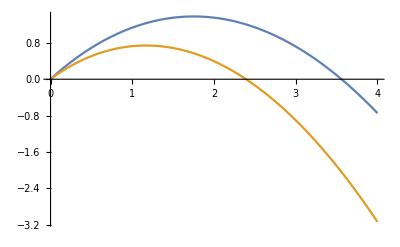

```mathematica
Plot[{-(g3 (144 (4 G3-9 π) π+19 g3 (11 G3+36 π)+2 √g3 √G3 (7 G3+216 π)))/(648 π^2)/.G3->1,-(g3 (144 (4 G3-9 π) π+19 g3 (11 G3+36 π)+2 √g3 √G3 (7 G3+216 π)))/(648 π^2)/.G3->2},{g3,0,4}]
```

```mathematica
(* for writing *)
2 √g3(β2+β3+β6+β7)/.NS->0/.etasp/.NS->0/.G4->G3/.g5->g3/.g4->g3//Simplify
```

-(g3^(3/2) (19 √g3 (11 G3+36 π)+2 √G3 (7 G3+216 π)))/(648 π^2)

```mathematica
-(g3^(3/2) (19 √g3 (11 G3+36 π)))/(648 π^2)//Apart
-(g3^(3/2) (2 √G3 (7 G3+216 π)))/(648 π^2)//Apart
```

-(209 g3^2 G3)/(648 π^2)-(19 g3^2)/(18 π)

-(7 g3^(3/2) G3^(3/2))/(324 π^2)-(2 g3^(3/2) √G3)/(3 π)

```mathematica
-(209 g3^2 G3)/(648 π^2)-(7 g3^(3/2) G3^(3/2))/(324 π^2)//Simplify
```

-(209 g3^2 G3+14 g3^(3/2) G3^(3/2))/(648 π^2)

```mathematica
s3sp=Solve[βg3pg0==0,g3]
```

{{g3→0},{g3→1/(361 (121 G3^2+792 G3 π+1296 π^2))2 (49 G3^3-57168 G3^2 π-14904 G3 π^2+443232 π^3-√(2401 G3^6-5602464 G3^5 π-356357232 G3^4 π^2-5663338560 G3^3 π^3-886837248 G3^2 π^4+41358864384 G3 π^5))},{g3→1/(361 (121 G3^2+792 G3 π+1296 π^2))2 (49 G3^3-57168 G3^2 π-14904 G3 π^2+443232 π^3+√(2401 G3^6-5602464 G3^5 π-356357232 G3^4 π^2-5663338560 G3^3 π^3-886837248 G3^2 π^4+41358864384 G3 π^5))}}

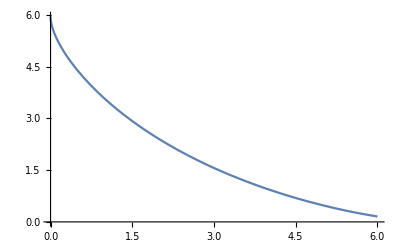

```mathematica
Plot[s3sp[[2,1,2]],{G3,0,6}]
```

```mathematica
(* pure gravity subcase *)
(* putting ηS=0 *)
(* "full" *)
(* keep separate G *)
```

```mathematica
etasf[[1,2]]/.g4->g3/.g5->g3/.G4->G3/.NS->0//Simplify
etasf[[2,2]]/.g4->g3/.g5->g3/.G4->G3/.NS->0//Simplify
```

(2 G3 (1591 G3-55296 π))/(2665 G3^2-3384 G3 π+124416 π^2)

(2 G3 (16195 G3+32832 π))/(2665 G3^2-3384 G3 π+124416 π^2)

```mathematica
(* note that anom dim for pure gravity are simply obtained by putting NS=0 *)
```

```mathematica
(2+ηTT)g3+2 √g3(β2+β3+β6+β7)
βg3pg0=%/.NS->0/.etasf/.NS->0/.G4->G3/.g5->g3/.g4->g3//Simplify
```

g3 (2+ηTT)+2 √g3 ((5 √G3 g4 (-8+ηTT))/(216 π)+(95 g5^(3/2) (-6+ηTT))/(648 π)+(19 g5^(3/2) (6-ησ))/(324 π)+(√G3 g4 (-8+ησ))/(54 π))

-(g3 (-288 π (532 G3^2-7335 G3 π+15552 π^2)+76 g3 (1345 G3^2+8658 G3 π+31104 π^2)+√g3 √G3 (7735 G3^2+7776 G3 π+1492992 π^2)))/(18 π (2665 G3^2-3384 G3 π+124416 π^2))

```mathematica
s3f=Solve[βg3pg0==0,g3];
```

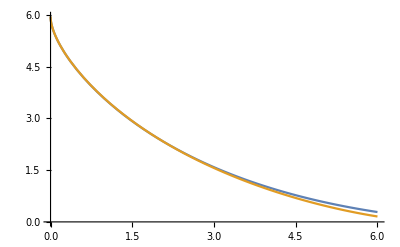

```mathematica
Plot[{s3f[[2,1,2]],s3sp[[2,1,2]]},{G3,0,6}]
```

```mathematica
(* recover previously found fixed point *)
NSolve[(βg3pg0/.G3->2.204),g3]
```

{{g3→2.20477},{g3→0.}}

```mathematica
D[βg3pg0,g3]/.{g3->2.204769706329456}
```

-(0.0389889 (76 (1345 G3^2+8658 G3 π+31104 π^2)+0.336735 √G3 (7735 G3^2+7776 G3 π+1492992 π^2)))/(2665 G3^2-3384 G3 π+124416 π^2)-(-288 π (532 G3^2-7335 G3 π+15552 π^2)+167.562 (1345 G3^2+8658 G3 π+31104 π^2)+1.48485 √G3 (7735 G3^2+7776 G3 π+1492992 π^2))/(18 π (2665 G3^2-3384 G3 π+124416 π^2))

```mathematica
etasfpg[[1,2]]/.same/.{g3->2.204769706329456}
etasfpg[[2,2]]/.same/.{g3->2.204769706329456}
```

Part::partd: Part specification etasfpg⟦1,2⟧ is longer than depth of object.

etasfpg⟦1,2⟧

Part::partd: Part specification etasfpg⟦2,2⟧ is longer than depth of object.

etasfpg⟦2,2⟧

```mathematica
(* pure gravity subcase *)
(* keeping ηS *)
(* "full" *)
(* keep separate G *)
```

```mathematica
etasf[[1,2]]/.g4->g3/.g5->g3/.G4->G3/.NS->0//Simplify
etasf[[2,2]]/.g4->g3/.g5->g3/.G4->G3/.NS->0//Simplify
etasf[[3,2]]/.g4->g3/.g5->g3/.G4->G3/.NS->0//Simplify
```

(2 G3 (1591 G3-55296 π))/(2665 G3^2-3384 G3 π+124416 π^2)

(2 G3 (16195 G3+32832 π))/(2665 G3^2-3384 G3 π+124416 π^2)

(2 g3 (37405 G3^2+147888 G3 π+1741824 π^2))/((g3+16 π) (2665 G3^2-3384 G3 π+124416 π^2))

```mathematica
(2+ηTT+ηS)g3+2 √g3(β2+β3+β6+β7)
βg3pg=%/.NS->0/.etasf/.NS->0/.g4->g3/.g5->g3/.G4->G3//Simplify
```

g3 (2+ηS+ηTT)+2 √g3 ((5 √G3 g4 (-8+ηTT))/(216 π)+(95 g5^(3/2) (-6+ηTT))/(648 π)+(19 g5^(3/2) (6-ησ))/(324 π)+(√G3 g4 (-8+ησ))/(54 π))

-((g3 (4 g3 π (33931 G3^2+1829160 G3 π-7340544 π^2)-4608 π^2 (532 G3^2-7335 G3 π+15552 π^2)+76 g3^2 (1345 G3^2+8658 G3 π+31104 π^2)+g3^(3/2) √G3 (7735 G3^2+7776 G3 π+1492992 π^2)+16 √g3 √G3 π (7735 G3^2+7776 G3 π+1492992 π^2)))/(18 π (g3+16 π) (2665 G3^2-3384 G3 π+124416 π^2)))

```mathematica
s3=Solve[βg3pg==0,g3]
```

{{g3→-(-59830225 G3^5+27627119840 G3^4 π+1651271784768 G3^3 π^2+4244470046208 G3^2 π^3-6278449397760 G3 π^4-138818730590208 π^5)/(23104 (1345 G3^2+8658 G3 π+31104 π^2)^2)-1/2 √1-1/2 √(((-59830225 G3^5+27627119840 G3^4 π+1+1-6278449397760 G3 π^4-138818730590208 π^5)^2)/(66724352 (1345 G3^2+8658 G3 π+31104 π^2)^4)-(π (1))/(361 (1)^2)-(π 1)/(1083 1)-1-1/1-(-(1)^3/(192699928576 (1)^6)-1/(361 1)+(π (1) (1))/(521284 1^4))/(4 √(5+1^1/1)))},3,{g3→0}}
 |  |  |  |

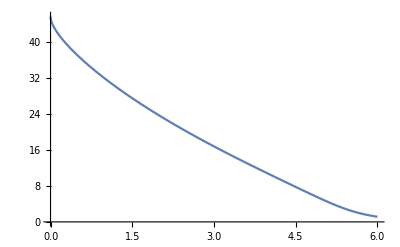

```mathematica
Plot[s3[[3,1,2]],{G3,0,6}]
```

```mathematica
(* recover previous fp *)
s3[[3,1,2]]/.G3->4.987
```

4.98956

```mathematica
D[βg3pg,g3]/.{g3->4.987395020385762}
```

-1/(2665 G3^2-3384 G3 π+124416 π^2)0.00159623 (4 π (33931 G3^2+1829160 G3 π-7340544 π^2)+758.084 (1345 G3^2+8658 G3 π+31104 π^2)+14.6038 √G3 (7735 G3^2+7776 G3 π+1492992 π^2))-1/(2665 G3^2-3384 G3 π+124416 π^2)0.000291164 (62.6735 (33931 G3^2+1829160 G3 π-7340544 π^2)-4608 π^2 (532 G3^2-7335 G3 π+15552 π^2)+1890.43 (1345 G3^2+8658 G3 π+31104 π^2)+123.393 √G3 (7735 G3^2+7776 G3 π+1492992 π^2))

```mathematica
etasfpg[[1,2]]/.same/.{g3->4.987395020385762}
etasfpg[[2,2]]/.same/.{g3->4.987395020385762}
```

Part::partd: Part specification etasfpg⟦1,2⟧ is longer than depth of object.

etasfpg⟦1,2⟧

Part::partd: Part specification etasfpg⟦2,2⟧ is longer than depth of object.

etasfpg⟦2,2⟧

```mathematica
(* background fixed point *)
βG=2G-G^2/π(15/8-5/18 ηTT+1/24 ησ-NS/24(4-ηS))/.ηTT->3.27/.ησ->-0.31/.ηS->-6.49/.NS->1
```

2 G-0.16446 G^2

```mathematica
NSolve[βG==0,G]
```

{{G→0.+0. ⅈ},{G→12.161}}

```mathematica
(* WITH SCALARS *)
```

```mathematica
etasf0/.same//Simplify
```

{ηTT→(2 g3 (g3 (1591+750 NS)+864 (-64+3 NS) π))/(2665 g3^2-3384 g3 π+124416 π^2),ησ→(2 g3 (-205 g3 (-79+6 NS)+1728 (19+6 NS) π))/(2665 g3^2-3384 g3 π+124416 π^2)}

```mathematica
etasf/.same//Simplify
```

{ηTT→-(4 g3 (g3^2 (1591-7941 NS+54 NS^2)+16 g3 (-1865+912 NS) π+13824 (-64+3 NS) π^2))/(5 g3^3 (-1066+759 NS)-16 g3^2 (4907+324 NS) π-140544 g3 π^2-3981312 π^3),ησ→-(4 g3 (5 g3^2 (3239-1689 NS+108 NS^2)-16 g3 (-18247+7386 NS) π+27648 (19+6 NS) π^2))/(5 g3^3 (-1066+759 NS)-16 g3^2 (4907+324 NS) π-140544 g3 π^2-3981312 π^3),ηS→(4 g3 (5 g3^2 (-7481+582 NS)+144 g3 (-1027+36 NS) π-1741824 π^2))/(5 g3^3 (-1066+759 NS)-16 g3^2 (4907+324 NS) π-140544 g3 π^2-3981312 π^3)}

```mathematica
(* with ηS=0 *)
```

```mathematica
βg3noetaS=βg3/.ηS->0/.etasf0/.g4->g3/.g5->g3/.G3->g3/.G4->g3;
Series[βg3noetaS,{g3,0,2}]//Simplify
```

2 g3+((-80+NS) g3^2)/(24 π)+O[g3]^3

```mathematica
NSolve[(βg3noetaS/.NS->1)==0,g3]
```

{{g3→-6.39864+27.2253 ⅈ},{g3→-6.39864-27.2253 ⅈ},{g3→1.82181},{g3→0.}}

```mathematica
tab1=Table[NSolve[(βg3noetaS/.NS->i)==0,g3][[3,1,2]],{i,1,30}]
```

{1.82181,1.8514,1.88224,1.91442,1.94804,1.98323,2.02013,2.05888,2.09966,2.14267,2.18814,2.23635,2.28761,2.3423,2.40086,2.46385,2.53194,2.60596,2.68701,2.77648,2.87626,2.989,3.11856,3.27095,3.45645,3.69524,4.03921,4.81981,4.95411-1.22301 ⅈ,4.72203-1.70672 ⅈ}

```mathematica
tab2=Table[ηTT/.etasf0/.same/.NS->i/.g3->tab1[[i]],{i,1,30}]
```

{-0.482787,-0.461437,-0.43929,-0.416289,-0.392373,-0.367472,-0.341507,-0.314391,-0.286024,-0.256293,-0.225066,-0.192195,-0.157502,-0.120782,-0.08179,-0.0402301,0.00425745,0.0521189,0.103918,0.160385,0.22249,0.29157,0.369559,0.459425,0.566161,0.69943,0.883575,1.2699,1.37889-0.559386 ⅈ,1.31801-0.801052 ⅈ}

```mathematica
tab3=Table[ησ/.etasf0/.same/.NS->i/.g3->tab1[[i]],{i,1,30}]
```

{0.487787,0.589212,0.693909,0.802087,0.913973,1.02982,1.14992,1.27457,1.40414,1.53902,1.67968,1.82664,1.98049,2.14195,2.31184,2.49116,2.68109,2.8831,3.09902,3.33118,3.58266,3.85764,4.16207,4.50498,4.90129,5.37941,6.00953,7.21625,7.69293-1.57062 ⅈ,7.69227-2.30133 ⅈ}

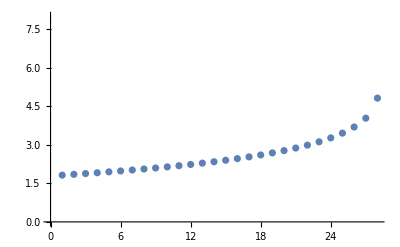

```mathematica
ListPlot[tab1,PlotRange->{0,8}]
```

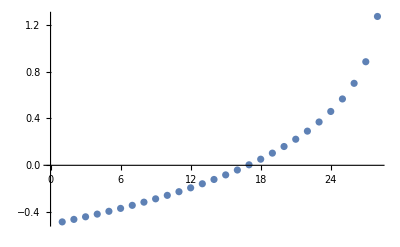

```mathematica
ListPlot[tab2]
```

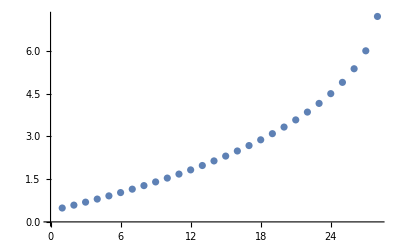

```mathematica
ListPlot[tab3]
```

```mathematica
(* with ηS=0 *)
(* semiperturbative *)
```

```mathematica
βg3/.ηS->0/.etasp/.same//Simplify
Series[%,{g3,0,2}]//Simplify
```

(g3 (g3^2 (-4023+148 NS)+540 g3 (-80+NS) π+25920 π^2))/(12960 π^2)

2 g3+((-80+NS) g3^2)/(24 π)+O[g3]^3

```mathematica
βg3/.ηS->0
βg3/.ηS->0/.same
βg3sp=βg3/.ηS->0/.etasp/.same//Simplify
```

g3 (2+ηTT)+√g3 g5^(3/2) (-19/(18 π)+(95 ηTT)/(324 π)-(19 ησ)/(162 π))+g3^(3/2) √G3 (3/(4 π)-ησ/(20 π))+g3^2 (3/(4 π)-ησ/(40 π))+√g3 √G3 g4 (-2/(3 π)+(5 ηTT)/(108 π)+ησ/(27 π))+g3 g4 (-20/(9 π)+(5 ησ)/(36 π))

g3 (2+ηTT)+g3^2 (-19/(18 π)+(95 ηTT)/(324 π)-(19 ησ)/(162 π))+g3^2 (3/(4 π)-ησ/(20 π))+g3^2 (3/(4 π)-ησ/(40 π))+g3^2 (-2/(3 π)+(5 ηTT)/(108 π)+ησ/(27 π))+g3^2 (-20/(9 π)+(5 ησ)/(36 π))

(g3 (g3^2 (-4023+148 NS)+540 g3 (-80+NS) π+25920 π^2))/(12960 π^2)

```mathematica
NSolve[(βg3sp/.NS->1)==0,g3]
```

{{}}

```mathematica
tab1spa=Table[NSolve[βg3sp==0,g3][[3,1,2]],{NS,1,27}]
```

Part::partw: Part 3 of {{}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧}

```mathematica
NSolve[(βg3sp/.NS->28)==0,g3]
```

{{}}

```mathematica
tab1spb=Table[NSolve[βg3sp==0,g3][[2,1,2]],{NS,28,60}]
```

Part::partw: Part 2 of {{}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧}

```mathematica
tab1sp=Join[tab1spa,tab1spb]
```

{{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦3,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧,{{}}⟦2,1,2⟧}

```mathematica
ListPlot[{tab1,tab1sp},PlotRange->{0,8}]
```

-Graphics-

```mathematica
tab2sp=Table[Simplify[ηTT/.etasp/.same]/.g3->tab1sp[[NS]],{NS,1,60}]
```

{-(61 {{}}⟦3,1,2⟧)/(72 π),-(29 {{}}⟦3,1,2⟧)/(36 π),-(55 {{}}⟦3,1,2⟧)/(72 π),-(13 {{}}⟦3,1,2⟧)/(18 π),-(49 {{}}⟦3,1,2⟧)/(72 π),-(23 {{}}⟦3,1,2⟧)/(36 π),-(43 {{}}⟦3,1,2⟧)/(72 π),-(5 {{}}⟦3,1,2⟧)/(9 π),-(37 {{}}⟦3,1,2⟧)/(72 π),-(17 {{}}⟦3,1,2⟧)/(36 π),-(31 {{}}⟦3,1,2⟧)/(72 π),-(7 {{}}⟦3,1,2⟧)/(18 π),-(25 {{}}⟦3,1,2⟧)/(72 π),-(11 {{}}⟦3,1,2⟧)/(36 π),-(19 {{}}⟦3,1,2⟧)/(72 π),-(2 {{}}⟦3,1,2⟧)/(9 π),-(13 {{}}⟦3,1,2⟧)/(72 π),-(5 {{}}⟦3,1,2⟧)/(36 π),-(7 {{}}⟦3,1,2⟧)/(72 π),-({{}}⟦3,1,2⟧)/(18 π),-({{}}⟦3,1,2⟧)/(72 π),({{}}⟦3,1,2⟧)/(36 π),(5 {{}}⟦3,1,2⟧)/(72 π),({{}}⟦3,1,2⟧)/(9 π),(11 {{}}⟦3,1,2⟧)/(72 π),(7 {{}}⟦3,1,2⟧)/(36 π),(17 {{}}⟦3,1,2⟧)/(72 π),(5 {{}}⟦2,1,2⟧)/(18 π),(23 {{}}⟦2,1,2⟧)/(72 π),(13 {{}}⟦2,1,2⟧)/(36 π),(29 {{}}⟦2,1,2⟧)/(72 π),(4 {{}}⟦2,1,2⟧)/(9 π),(35 {{}}⟦2,1,2⟧)/(72 π),(19 {{}}⟦2,1,2⟧)/(36 π),(41 {{}}⟦2,1,2⟧)/(72 π),(11 {{}}⟦2,1,2⟧)/(18 π),(47 {{}}⟦2,1,2⟧)/(72 π),(25 {{}}⟦2,1,2⟧)/(36 π),(53 {{}}⟦2,1,2⟧)/(72 π),(7 {{}}⟦2,1,2⟧)/(9 π),(59 {{}}⟦2,1,2⟧)/(72 π),(31 {{}}⟦2,1,2⟧)/(36 π),(65 {{}}⟦2,1,2⟧)/(72 π),(17 {{}}⟦2,1,2⟧)/(18 π),(71 {{}}⟦2,1,2⟧)/(72 π),(37 {{}}⟦2,1,2⟧)/(36 π),(77 {{}}⟦2,1,2⟧)/(72 π),(10 {{}}⟦2,1,2⟧)/(9 π),(83 {{}}⟦2,1,2⟧)/(72 π),(43 {{}}⟦2,1,2⟧)/(36 π),(89 {{}}⟦2,1,2⟧)/(72 π),(23 {{}}⟦2,1,2⟧)/(18 π),(95 {{}}⟦2,1,2⟧)/(72 π),(49 {{}}⟦2,1,2⟧)/(36 π),(101 {{}}⟦2,1,2⟧)/(72 π),(13 {{}}⟦2,1,2⟧)/(9 π),(107 {{}}⟦2,1,2⟧)/(72 π),(55 {{}}⟦2,1,2⟧)/(36 π),(113 {{}}⟦2,1,2⟧)/(72 π),(29 {{}}⟦2,1,2⟧)/(18 π)}

```mathematica
tab3sp=Table[Simplify[ησ/.etasp/.same]/.g3->tab1sp[[NS]],{NS,1,60}]
```

{(25 {{}}⟦3,1,2⟧)/(36 π),(31 {{}}⟦3,1,2⟧)/(36 π),(37 {{}}⟦3,1,2⟧)/(36 π),(43 {{}}⟦3,1,2⟧)/(36 π),(49 {{}}⟦3,1,2⟧)/(36 π),(55 {{}}⟦3,1,2⟧)/(36 π),(61 {{}}⟦3,1,2⟧)/(36 π),(67 {{}}⟦3,1,2⟧)/(36 π),(73 {{}}⟦3,1,2⟧)/(36 π),(79 {{}}⟦3,1,2⟧)/(36 π),(85 {{}}⟦3,1,2⟧)/(36 π),(91 {{}}⟦3,1,2⟧)/(36 π),(97 {{}}⟦3,1,2⟧)/(36 π),(103 {{}}⟦3,1,2⟧)/(36 π),(109 {{}}⟦3,1,2⟧)/(36 π),(115 {{}}⟦3,1,2⟧)/(36 π),(121 {{}}⟦3,1,2⟧)/(36 π),(127 {{}}⟦3,1,2⟧)/(36 π),(133 {{}}⟦3,1,2⟧)/(36 π),(139 {{}}⟦3,1,2⟧)/(36 π),(145 {{}}⟦3,1,2⟧)/(36 π),(151 {{}}⟦3,1,2⟧)/(36 π),(157 {{}}⟦3,1,2⟧)/(36 π),(163 {{}}⟦3,1,2⟧)/(36 π),(169 {{}}⟦3,1,2⟧)/(36 π),(175 {{}}⟦3,1,2⟧)/(36 π),(181 {{}}⟦3,1,2⟧)/(36 π),(187 {{}}⟦2,1,2⟧)/(36 π),(193 {{}}⟦2,1,2⟧)/(36 π),(199 {{}}⟦2,1,2⟧)/(36 π),(205 {{}}⟦2,1,2⟧)/(36 π),(211 {{}}⟦2,1,2⟧)/(36 π),(217 {{}}⟦2,1,2⟧)/(36 π),(223 {{}}⟦2,1,2⟧)/(36 π),(229 {{}}⟦2,1,2⟧)/(36 π),(235 {{}}⟦2,1,2⟧)/(36 π),(241 {{}}⟦2,1,2⟧)/(36 π),(247 {{}}⟦2,1,2⟧)/(36 π),(253 {{}}⟦2,1,2⟧)/(36 π),(259 {{}}⟦2,1,2⟧)/(36 π),(265 {{}}⟦2,1,2⟧)/(36 π),(271 {{}}⟦2,1,2⟧)/(36 π),(277 {{}}⟦2,1,2⟧)/(36 π),(283 {{}}⟦2,1,2⟧)/(36 π),(289 {{}}⟦2,1,2⟧)/(36 π),(295 {{}}⟦2,1,2⟧)/(36 π),(301 {{}}⟦2,1,2⟧)/(36 π),(307 {{}}⟦2,1,2⟧)/(36 π),(313 {{}}⟦2,1,2⟧)/(36 π),(319 {{}}⟦2,1,2⟧)/(36 π),(325 {{}}⟦2,1,2⟧)/(36 π),(331 {{}}⟦2,1,2⟧)/(36 π),(337 {{}}⟦2,1,2⟧)/(36 π),(343 {{}}⟦2,1,2⟧)/(36 π),(349 {{}}⟦2,1,2⟧)/(36 π),(355 {{}}⟦2,1,2⟧)/(36 π),(361 {{}}⟦2,1,2⟧)/(36 π),(367 {{}}⟦2,1,2⟧)/(36 π),(373 {{}}⟦2,1,2⟧)/(36 π),(379 {{}}⟦2,1,2⟧)/(36 π)}

```mathematica
ListPlot[{tab2,tab2sp}]
```

-Graphics-

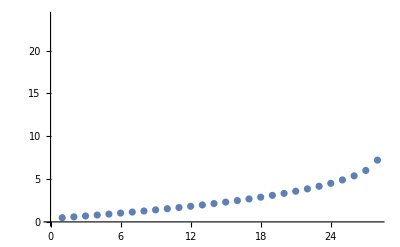

```mathematica
ListPlot[{tab3,tab3sp},PlotRange->{0,24}]
```

```mathematica
(* with ηS nonzero *)
```

```mathematica
(* full *)
```

```mathematica
βg3
```

g3 (2+2 ηS+ηTT)+√g3 g5^(3/2) (-19/(18 π)+(95 ηTT)/(324 π)-(19 ησ)/(162 π))+g3^(3/2) √G3 (3/(4 π)-ηS/(40 π)-ησ/(20 π))+g3^2 (3/(4 π)-ηS/(20 π)-ησ/(40 π))+√g3 √G3 g4 (-2/(3 π)+(5 ηTT)/(108 π)+ησ/(27 π))+g3 g4 (-20/(9 π)+(5 ηS)/(36 π)+(5 ησ)/(36 π))

```mathematica
βg3noetaS=βg3/.etasf/.g4->g3/.g5->g3/.G3->g3/.G4->g3;
Series[βg3noetaS,{g3,0,2}]//Simplify
```

2 g3+((4+NS) g3^2)/(24 π)+O[g3]^3

```mathematica
(* for writing *)
Series[βg3/.ηTT->(ηTT/.etasf)/.ησ->(ησ/.etasf)/.same,{g3,0,2}]//Apart
```

(2+2 ηS) g3+((-1200+15 NS+23 ηS) g3^2)/(360 π)+O[g3]^3

```mathematica
%/.ηS->(ηS/.etasf)/.same
```

2 g3+((4+NS) g3^2)/(24 π)+O[g3]^3

```mathematica
-6π(-1200+15 NS+23 ηS)/(360π)//Expand
```

20-NS/4-(23 ηS)/60

```mathematica
Series[ηS/.etasf/.same,{g3,0,1}]
```

(7 g3)/(4 π)+O[g3]^2

```mathematica
(2+2 ηS) g3+((-1200+15 NS) g3^2)/(360 π)/.NS->1
```

-(79 g3^2)/(24 π)+g3 (2+2 ηS)

```mathematica
2g3 ηS/.ηS->(7 g3)/(4 π)//N
```

1.11408 g3^2

```mathematica
((-1200+15 NS) g3^2)/(360 π)/.NS->1//N
```

-1.04777 g3^2

```mathematica
2 g3+((-1200+15 NS) g3^2)/(360 π)
```

2 g3+(g3^2 (-1200+15 NS))/(360 π)

```mathematica
Solve[1200-15 NS==0,NS]
```

{{NS→80}}

```mathematica
ba=(2+2 ηS) g3+((-1200+15 NS+23 ηS) g3^2)/(360 π)/.ηS->(7 g3)/(4 π)
```

g3 (2+(7 g3)/(2 π))+(g3^2 (-1200+15 NS+(161 g3)/(4 π)))/(360 π)

```mathematica
2 ηS g3+((-1200+15 NS) g3^2)/(360 π)/.ηS->(7 g3)/(4 π)//Simplify
```

(g3^2 (4+NS))/(24 π)

```mathematica
Solve[ba==0,g3]
```

{{g3→0},{g3→6/161 (-20-5 NS-√5 √(-2496+40 NS+5 NS^2)) π},{g3→6/161 (-20-5 NS+√5 √(-2496+40 NS+5 NS^2)) π}}

```mathematica
(* complex *)
```

```mathematica
βg3
```

g3 (2+2 ηS+ηTT)+√g3 g5^(3/2) (-19/(18 π)+(95 ηTT)/(324 π)-(19 ησ)/(162 π))+g3^(3/2) √G3 (3/(4 π)-ηS/(40 π)-ησ/(20 π))+g3^2 (3/(4 π)-ηS/(20 π)-ησ/(40 π))+√g3 √G3 g4 (-2/(3 π)+(5 ηTT)/(108 π)+ησ/(27 π))+g3 g4 (-20/(9 π)+(5 ηS)/(36 π)+(5 ησ)/(36 π))

```mathematica
B3[NS_]=βg3/.etasf/.same//Simplify
```

(g3 (5 g3^4 (-42640-30573 NS+684 NS^2)+20 g3^3 (461308-220869 NS+972 NS^2) π+576 g3^2 (13513+11364 NS) π^2+414720 g3 (205+36 NS) π^3+716636160 π^4))/(90 π (g3^3 (5330-3795 NS)+16 g3^2 (4907+324 NS) π+140544 g3 π^2+3981312 π^3))

```mathematica
Solve[(B3[NS])==0,g3]
```

{{g3→0},{g3→-(461308 π-220869 NS π+972 NS^2 π)/(-42640-30573 NS+684 NS^2)-1/2 √((4 (461308 π-220869 NS π+972 NS^2 π)^2)/((-42640-30573 NS+684 NS^2)^2)-(384 (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2))+(110592 2^(1/3) (-12436153331-1504808061 NS+799188696 NS^2-2624400 NS^3) π^4)/(5 (-42640-30573 NS+684 NS^2) (1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3))+(1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3)/(15 2^(1/3) (-42640-30573 NS+684 NS^2)))-1/2 √((8 (461308 π-220869 NS π+972 NS^2 π)^2)/((-42640-30573 NS+684 NS^2)^2)-(768 (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2))-(110592 2^(1/3) (-12436153331-1504808061 NS+799188696 NS^2-2624400 NS^3) π^4)/(5 (-42640-30573 NS+684 NS^2) (1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3))-(1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3)/(15 2^(1/3) (-42640-30573 NS+684 NS^2))-(-(64 (461308 π-220869 NS π+972 NS^2 π)^3)/((-42640-30573 NS+684 NS^2)^3)+(9216 (461308 π-220869 NS π+972 NS^2 π) (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2)^2)-(663552 (205 π^3+36 NS π^3))/(-42640-30573 NS+684 NS^2))/(4 √((4 (461308 π-220869 NS π+972 NS^2 π)^2)/((-42640-30573 NS+684 NS^2)^2)-(384 (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2))+(110592 2^(1/3) (-12436153331-1504808061 NS+799188696 NS^2-2624400 NS^3) π^4)/(5 (-42640-30573 NS+684 NS^2) (1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3))+(1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3)/(15 2^(1/3) (-42640-30573 NS+684 NS^2)))))},{g3→-(461308 π-220869 NS π+972 NS^2 π)/(-42640-30573 NS+684 NS^2)-1/2 √((4 (461308 π-220869 NS π+972 NS^2 π)^2)/((-42640-30573 NS+684 NS^2)^2)-(384 (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2))+(110592 2^(1/3) (-12436153331-1504808061 NS+799188696 NS^2-2624400 NS^3) π^4)/(5 (-42640-30573 NS+684 NS^2) (1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3))+(1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3)/(15 2^(1/3) (-42640-30573 NS+684 NS^2)))+1/2 √((8 (461308 π-220869 NS π+972 NS^2 π)^2)/((-42640-30573 NS+684 NS^2)^2)-(768 (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2))-(110592 2^(1/3) (-12436153331-1504808061 NS+799188696 NS^2-2624400 NS^3) π^4)/(5 (-42640-30573 NS+684 NS^2) (1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3))-(1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3)/(15 2^(1/3) (-42640-30573 NS+684 NS^2))-(-(64 (461308 π-220869 NS π+972 NS^2 π)^3)/((-42640-30573 NS+684 NS^2)^3)+(9216 (461308 π-220869 NS π+972 NS^2 π) (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2)^2)-(663552 (205 π^3+36 NS π^3))/(-42640-30573 NS+684 NS^2))/(4 √((4 (461308 π-220869 NS π+972 NS^2 π)^2)/((-42640-30573 NS+684 NS^2)^2)-(384 (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2))+(110592 2^(1/3) (-12436153331-1504808061 NS+799188696 NS^2-2624400 NS^3) π^4)/(5 (-42640-30573 NS+684 NS^2) (1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3))+(1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3)/(15 2^(1/3) (-42640-30573 NS+684 NS^2)))))},{g3→-(461308 π-220869 NS π+972 NS^2 π)/(-42640-30573 NS+684 NS^2)+1/2 √((4 (461308 π-220869 NS π+972 NS^2 π)^2)/((-42640-30573 NS+684 NS^2)^2)-(384 (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2))+(110592 2^(1/3) (-12436153331-1504808061 NS+799188696 NS^2-2624400 NS^3) π^4)/(5 (-42640-30573 NS+684 NS^2) (1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3))+(1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3)/(15 2^(1/3) (-42640-30573 NS+684 NS^2)))-1/2 √((8 (461308 π-220869 NS π+972 NS^2 π)^2)/((-42640-30573 NS+684 NS^2)^2)-(768 (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2))-(110592 2^(1/3) (-12436153331-1504808061 NS+799188696 NS^2-2624400 NS^3) π^4)/(5 (-42640-30573 NS+684 NS^2) (1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3))-(1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3)/(15 2^(1/3) (-42640-30573 NS+684 NS^2))+(-(64 (461308 π-220869 NS π+972 NS^2 π)^3)/((-42640-30573 NS+684 NS^2)^3)+(9216 (461308 π-220869 NS π+972 NS^2 π) (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2)^2)-(663552 (205 π^3+36 NS π^3))/(-42640-30573 NS+684 NS^2))/(4 √((4 (461308 π-220869 NS π+972 NS^2 π)^2)/((-42640-30573 NS+684 NS^2)^2)-(384 (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2))+(110592 2^(1/3) (-12436153331-1504808061 NS+799188696 NS^2-2624400 NS^3) π^4)/(5 (-42640-30573 NS+684 NS^2) (1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3))+(1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3)/(15 2^(1/3) (-42640-30573 NS+684 NS^2)))))},{g3→-(461308 π-220869 NS π+972 NS^2 π)/(-42640-30573 NS+684 NS^2)+1/2 √((4 (461308 π-220869 NS π+972 NS^2 π)^2)/((-42640-30573 NS+684 NS^2)^2)-(384 (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2))+(110592 2^(1/3) (-12436153331-1504808061 NS+799188696 NS^2-2624400 NS^3) π^4)/(5 (-42640-30573 NS+684 NS^2) (1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3))+(1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3)/(15 2^(1/3) (-42640-30573 NS+684 NS^2)))+1/2 √((8 (461308 π-220869 NS π+972 NS^2 π)^2)/((-42640-30573 NS+684 NS^2)^2)-(768 (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2))-(110592 2^(1/3) (-12436153331-1504808061 NS+799188696 NS^2-2624400 NS^3) π^4)/(5 (-42640-30573 NS+684 NS^2) (1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3))-(1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3)/(15 2^(1/3) (-42640-30573 NS+684 NS^2))+(-(64 (461308 π-220869 NS π+972 NS^2 π)^3)/((-42640-30573 NS+684 NS^2)^3)+(9216 (461308 π-220869 NS π+972 NS^2 π) (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2)^2)-(663552 (205 π^3+36 NS π^3))/(-42640-30573 NS+684 NS^2))/(4 √((4 (461308 π-220869 NS π+972 NS^2 π)^2)/((-42640-30573 NS+684 NS^2)^2)-(384 (13513 π^2+11364 NS π^2))/(5 (-42640-30573 NS+684 NS^2))+(110592 2^(1/3) (-12436153331-1504808061 NS+799188696 NS^2-2624400 NS^3) π^4)/(5 (-42640-30573 NS+684 NS^2) (1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3))+(1637053120240655984492544 π^6-1515386648352765481058304 NS π^6+444182709168111498559488 NS^2 π^6-835380239695412723712 NS^3 π^6+10796951837815603200 NS^4 π^6+√(2960908483277851168350897596701651138164817920000 π^12-4859544110996412383848578689597035576806290227200 NS π^12+3708872120913160543966605892262540060218569523200 NS^2 π^12-1361385351553407523704779427564115085655382425600 NS^3 π^12+202596399923323249276504404683512220994030796800 NS^4 π^12-373896155608903475254370672682611920758374400 NS^5 π^12-67005661432304475040922934622574166304358400 NS^6 π^12+721092696147419049630860295919714172928000 NS^7 π^12-2295693728133635525809998486023700480000 NS^8 π^12+2640492748413577099820018958336000000 NS^9 π^12))^(1/3)/(15 2^(1/3) (-42640-30573 NS+684 NS^2)))))}}

```mathematica
fs1=NSolve[(B3[1])==0,g3]
```

{{g3→53.393},{g3→1.15771+16.074 ⅈ},{g3→1.15771-16.074 ⅈ},{g3→-13.8815},{g3→0.}}

```mathematica
D[B3[1],g3]/.{g3->-13.881523450149748}
```

-3.84995

```mathematica
ηTT/.etasf/.same/.NS->1/.{g3->-13.881523450149748}
ησ/.etasf/.same/.NS->1/.{g3->-13.881523450149748}
ηS/.etasf/.same/.NS->1/.{g3->-13.881523450149748}
```

3.26741

-0.309741

-6.48804

```mathematica
D[B3[1],g3]/.{g3->53.39297004073188}
```

-11.6544

```mathematica
ηTT/.etasf/.same/.NS->1/.{g3->53.39297004073188}
ησ/.etasf/.same/.NS->1/.{g3->53.39297004073188}
ηS/.etasf/.same/.NS->1/.{g3->53.39297004073188}
```

-5.21458

10.7811

25.2266

```mathematica
fs2=NSolve[(B3[2])==0,g3]
```

{{g3→29.7842},{g3→-19.0491},{g3→-3.90898+15.1076 ⅈ},{g3→-3.90898-15.1076 ⅈ},{g3→0.}}

```mathematica
D[B3[2],g3]/.fs2[[1]]
```

-10.0461

```mathematica
ηTT/.etasf/.same/.NS->1/.fs2[[1]]
ησ/.etasf/.same/.NS->1/.fs2[[1]]
ηS/.etasf/.same/.NS->1/.fs2[[1]]
```

-4.16563

8.26793

16.6098

```mathematica
fs3=NSolve[(B3[3])==0,g3]
```

{{g3→-30.0025},{g3→22.3477},{g3→-5.60947+11.4435 ⅈ},{g3→-5.60947-11.4435 ⅈ},{g3→0.}}

```mathematica
D[B3[3],g3]/.fs3[[2]]
```

-10.3238

```mathematica
ηTT/.etasf/.same/.NS->1/.fs3[[2]]
ησ/.etasf/.same/.NS->1/.fs3[[2]]
ηS/.etasf/.same/.NS->1/.fs3[[2]]
```

-3.70012

6.83577

13.1145

```mathematica
Table[NSolve[(B3[NS])==0,g3],{NS,1,95}]
```

{{{g3→53.393},{g3→1.15771+16.074 ⅈ},{g3→1.15771-16.074 ⅈ},{g3→-13.8815},{g3→0.}},{{g3→29.7842},{g3→-19.0491},{g3→-3.90898+15.1076 ⅈ},{g3→-3.90898-15.1076 ⅈ},{g3→0.}},{{g3→-30.0025},{g3→22.3477},{g3→-5.60947+11.4435 ⅈ},{g3→-5.60947-11.4435 ⅈ},{g3→0.}},{{g3→-41.5492},{g3→19.0164},{g3→-5.32477+9.29497 ⅈ},{g3→-5.32477-9.29497 ⅈ},{g3→0.}},{{g3→-50.8463},{g3→17.1215},{g3→-4.92871+8.09936 ⅈ},{g3→-4.92871-8.09936 ⅈ},{g3→0.}},{{g3→-58.3761},{g3→15.8878},{g3→-4.609+7.31301 ⅈ},{g3→-4.609-7.31301 ⅈ},{g3→0.}},{{g3→-64.7103},{g3→15.0153},{g3→-4.35721+6.73867 ⅈ},{g3→-4.35721-6.73867 ⅈ},{g3→0.}},{{g3→-70.2374},{g3→14.3638},{g3→-4.1552+6.29114 ⅈ},{g3→-4.1552-6.29114 ⅈ},{g3→0.}},{{g3→-75.2154},{g3→13.8581},{g3→-3.98953+5.92705 ⅈ},{g3→-3.98953-5.92705 ⅈ},{g3→0.}},{{g3→-79.8206},{g3→13.4547},{g3→-3.85099+5.62166 ⅈ},{g3→-3.85099-5.62166 ⅈ},{g3→0.}},{{g3→-84.1788},{g3→13.1259},{g3→-3.73325+5.35957 ⅈ},{g3→-3.73325-5.35957 ⅈ},{g3→0.}},{{g3→-88.3834},{g3→12.8536},{g3→-3.63179+5.13066 ⅈ},{g3→-3.63179-5.13066 ⅈ},{g3→0.}},{{g3→-92.5067},{g3→12.6252},{g3→-3.54335+4.92788 ⅈ},{g3→-3.54335-4.92788 ⅈ},{g3→0.}},{{g3→-96.6074},{g3→12.4318},{g3→-3.46551+4.74617 ⅈ},{g3→-3.46551-4.74617 ⅈ},{g3→0.}},{{g3→-100.735},{g3→12.2669},{g3→-3.39643+4.58179 ⅈ},{g3→-3.39643-4.58179 ⅈ},{g3→0.}},{{g3→-104.935},{g3→12.1253},{g3→-3.33467+4.43187 ⅈ},{g3→-3.33467-4.43187 ⅈ},{g3→0.}},{{g3→-109.247},{g3→12.0034},{g3→-3.27911+4.29419 ⅈ},{g3→-3.27911-4.29419 ⅈ},{g3→0.}},{{g3→-113.711},{g3→11.8981},{g3→-3.22886+4.16699 ⅈ},{g3→-3.22886-4.16699 ⅈ},{g3→0.}},{{g3→-118.367},{g3→11.8071},{g3→-3.18317+4.04885 ⅈ},{g3→-3.18317-4.04885 ⅈ},{g3→0.}},{{g3→-123.258},{g3→11.7285},{g3→-3.14147+3.9386 ⅈ},{g3→-3.14147-3.9386 ⅈ},{g3→0.}},{{g3→-128.428},{g3→11.6607},{g3→-3.10325+3.8353 ⅈ},{g3→-3.10325-3.8353 ⅈ},{g3→0.}},{{g3→-133.925},{g3→11.6024},{g3→-3.06809+3.73814 ⅈ},{g3→-3.06809-3.73814 ⅈ},{g3→0.}},{{g3→-139.806},{g3→11.5525},{g3→-3.03566+3.64646 ⅈ},{g3→-3.03566-3.64646 ⅈ},{g3→0.}},{{g3→-146.134},{g3→11.5103},{g3→-3.00565+3.55966 ⅈ},{g3→-3.00565-3.55966 ⅈ},{g3→0.}},{{g3→-152.982},{g3→11.4749},{g3→-2.97782+3.47727 ⅈ},{g3→-2.97782-3.47727 ⅈ},{g3→0.}},{{g3→-160.437},{g3→11.4457},{g3→-2.95194+3.39886 ⅈ},{g3→-2.95194-3.39886 ⅈ},{g3→0.}},{{g3→-168.602},{g3→11.4221},{g3→-2.92783+3.32406 ⅈ},{g3→-2.92783-3.32406 ⅈ},{g3→0.}},{{g3→-177.604},{g3→11.4037},{g3→-2.90532+3.25254 ⅈ},{g3→-2.90532-3.25254 ⅈ},{g3→0.}},{{g3→-187.594},{g3→11.3901},{g3→-2.88426+3.18402 ⅈ},{g3→-2.88426-3.18402 ⅈ},{g3→0.}},{{g3→-198.766},{g3→11.381},{g3→-2.86454+3.11825 ⅈ},{g3→-2.86454-3.11825 ⅈ},{g3→0.}},{{g3→-211.359},{g3→11.376},{g3→-2.84603+3.05501 ⅈ},{g3→-2.84603-3.05501 ⅈ},{g3→0.}},{{g3→-225.683},{g3→11.3748},{g3→-2.82864+2.9941 ⅈ},{g3→-2.82864-2.9941 ⅈ},{g3→0.}},{{g3→-242.14},{g3→11.3773},{g3→-2.81229+2.93533 ⅈ},{g3→-2.81229-2.93533 ⅈ},{g3→0.}},{{g3→-261.267},{g3→11.3833},{g3→-2.79688+2.87856 ⅈ},{g3→-2.79688-2.87856 ⅈ},{g3→0.}},{{g3→-283.793},{g3→11.3925},{g3→-2.78236+2.82362 ⅈ},{g3→-2.78236-2.82362 ⅈ},{g3→0.}},{{g3→-310.738},{g3→11.4049},{g3→-2.76865+2.7704 ⅈ},{g3→-2.76865-2.7704 ⅈ},{g3→0.}},{{g3→-343.569},{g3→11.4203},{g3→-2.7557+2.71878 ⅈ},{g3→-2.7557-2.71878 ⅈ},{g3→0.}},{{g3→-384.486},{g3→11.4386},{g3→-2.74345+2.66863 ⅈ},{g3→-2.74345-2.66863 ⅈ},{g3→0.}},{{g3→-436.932},{g3→11.4596},{g3→-2.73187+2.61987 ⅈ},{g3→-2.73187-2.61987 ⅈ},{g3→0.}},{{g3→-506.63},{g3→11.4834},{g3→-2.7209+2.57241 ⅈ},{g3→-2.7209-2.57241 ⅈ},{g3→0.}},{{g3→-603.83},{g3→11.5098},{g3→-2.71051+2.52615 ⅈ},{g3→-2.71051-2.52615 ⅈ},{g3→0.}},{{g3→-748.904},{g3→11.5387},{g3→-2.70066+2.48103 ⅈ},{g3→-2.70066-2.48103 ⅈ},{g3→0.}},{{g3→-988.933},{g3→11.5703},{g3→-2.69132+2.43697 ⅈ},{g3→-2.69132-2.43697 ⅈ},{g3→0.}},{{g3→-1462.81},{g3→11.6043},{g3→-2.68245+2.3939 ⅈ},{g3→-2.68245-2.3939 ⅈ},{g3→0.}},{{g3→-2838.01},{g3→11.6407},{g3→-2.67404+2.35176 ⅈ},{g3→-2.67404-2.35176 ⅈ},{g3→0.}},{{g3→-58066.3},{g3→11.6797},{g3→-2.66605+2.3105 ⅈ},{g3→-2.66605-2.3105 ⅈ},{g3→0.}},{{g3→3105.61},{g3→11.721},{g3→-2.65847+2.27006 ⅈ},{g3→-2.65847-2.27006 ⅈ},{g3→0.}},{{g3→1502.62},{g3→11.7648},{g3→-2.65126+2.23038 ⅈ},{g3→-2.65126-2.23038 ⅈ},{g3→0.}},{{g3→986.68},{g3→11.8111},{g3→-2.64441+2.19144 ⅈ},{g3→-2.64441-2.19144 ⅈ},{g3→0.}},{{g3→731.956},{g3→11.8598},{g3→-2.63791+2.15317 ⅈ},{g3→-2.63791-2.15317 ⅈ},{g3→0.}},{{g3→580.104},{g3→11.9109},{g3→-2.63173+2.11553 ⅈ},{g3→-2.63173-2.11553 ⅈ},{g3→0.}},{{g3→479.248},{g3→11.9646},{g3→-2.62585+2.0785 ⅈ},{g3→-2.62585-2.0785 ⅈ},{g3→0.}},{{g3→407.372},{g3→12.0208},{g3→-2.62027+2.04202 ⅈ},{g3→-2.62027-2.04202 ⅈ},{g3→0.}},{{g3→353.54},{g3→12.0796},{g3→-2.61497+2.00606 ⅈ},{g3→-2.61497-2.00606 ⅈ},{g3→0.}},{{g3→311.703},{g3→12.1411},{g3→-2.60993+1.9706 ⅈ},{g3→-2.60993-1.9706 ⅈ},{g3→0.}},{{g3→278.244},{g3→12.2052},{g3→-2.60515+1.93559 ⅈ},{g3→-2.60515-1.93559 ⅈ},{g3→0.}},{{g3→250.867},{g3→12.2721},{g3→-2.60061+1.901 ⅈ},{g3→-2.60061-1.901 ⅈ},{g3→0.}},{{g3→228.046},{g3→12.3418},{g3→-2.59629+1.86681 ⅈ},{g3→-2.59629-1.86681 ⅈ},{g3→0.}},{{g3→208.725},{g3→12.4145},{g3→-2.5922+1.83298 ⅈ},{g3→-2.5922-1.83298 ⅈ},{g3→0.}},{{g3→192.15},{g3→12.4902},{g3→-2.58833+1.79948 ⅈ},{g3→-2.58833-1.79948 ⅈ},{g3→0.}},{{g3→177.771},{g3→12.569},{g3→-2.58465+1.7663 ⅈ},{g3→-2.58465-1.7663 ⅈ},{g3→0.}},{{g3→165.175},{g3→12.6511},{g3→-2.58117+1.7334 ⅈ},{g3→-2.58117-1.7334 ⅈ},{g3→0.}},{{g3→154.044},{g3→12.7366},{g3→-2.57787+1.70075 ⅈ},{g3→-2.57787-1.70075 ⅈ},{g3→0.}},{{g3→144.135},{g3→12.8257},{g3→-2.57476+1.66833 ⅈ},{g3→-2.57476-1.66833 ⅈ},{g3→0.}},{{g3→135.252},{g3→12.9184},{g3→-2.57182+1.63611 ⅈ},{g3→-2.57182-1.63611 ⅈ},{g3→0.}},{{g3→127.242},{g3→13.0151},{g3→-2.56904+1.60407 ⅈ},{g3→-2.56904-1.60407 ⅈ},{g3→0.}},{{g3→119.979},{g3→13.1159},{g3→-2.56642+1.57217 ⅈ},{g3→-2.56642-1.57217 ⅈ},{g3→0.}},{{g3→113.36},{g3→13.221},{g3→-2.56396+1.54041 ⅈ},{g3→-2.56396-1.54041 ⅈ},{g3→0.}},{{g3→107.3},{g3→13.3307},{g3→-2.56164+1.50874 ⅈ},{g3→-2.56164-1.50874 ⅈ},{g3→0.}},{{g3→101.729},{g3→13.4452},{g3→-2.55947+1.47715 ⅈ},{g3→-2.55947-1.47715 ⅈ},{g3→0.}},{{g3→96.5872},{g3→13.5649},{g3→-2.55743+1.4456 ⅈ},{g3→-2.55743-1.4456 ⅈ},{g3→0.}},{{g3→91.8238},{g3→13.6902},{g3→-2.55553+1.41407 ⅈ},{g3→-2.55553-1.41407 ⅈ},{g3→0.}},{{g3→87.396},{g3→13.8214},{g3→-2.55375+1.38254 ⅈ},{g3→-2.55375-1.38254 ⅈ},{g3→0.}},{{g3→83.2669},{g3→13.9589},{g3→-2.5521+1.35096 ⅈ},{g3→-2.5521-1.35096 ⅈ},{g3→0.}},{{g3→79.4044},{g3→14.1033},{g3→-2.55057+1.31931 ⅈ},{g3→-2.55057-1.31931 ⅈ},{g3→0.}},{{g3→75.7807},{g3→14.2552},{g3→-2.54916+1.28756 ⅈ},{g3→-2.54916-1.28756 ⅈ},{g3→0.}},{{g3→72.3713},{g3→14.4151},{g3→-2.54786+1.25567 ⅈ},{g3→-2.54786-1.25567 ⅈ},{g3→0.}},{{g3→69.1547},{g3→14.584},{g3→-2.54667+1.2236 ⅈ},{g3→-2.54667-1.2236 ⅈ},{g3→0.}},{{g3→66.1118},{g3→14.7625},{g3→-2.54558+1.19133 ⅈ},{g3→-2.54558-1.19133 ⅈ},{g3→0.}},{{g3→63.2253},{g3→14.9518},{g3→-2.5446+1.15879 ⅈ},{g3→-2.5446-1.15879 ⅈ},{g3→0.}},{{g3→60.4799},{g3→15.1531},{g3→-2.54371+1.12596 ⅈ},{g3→-2.54371-1.12596 ⅈ},{g3→0.}},{{g3→57.8612},{g3→15.3677},{g3→-2.54293+1.09277 ⅈ},{g3→-2.54293-1.09277 ⅈ},{g3→0.}},{{g3→55.3564},{g3→15.5975},{g3→-2.54223+1.05917 ⅈ},{g3→-2.54223-1.05917 ⅈ},{g3→0.}},{{g3→52.9532},{g3→15.8445},{g3→-2.54163+1.02509 ⅈ},{g3→-2.54163-1.02509 ⅈ},{g3→0.}},{{g3→50.6398},{g3→16.1113},{g3→-2.54112+0.990466 ⅈ},{g3→-2.54112-0.990466 ⅈ},{g3→0.}},{{g3→48.4048},{g3→16.4011},{g3→-2.54069+0.955213 ⅈ},{g3→-2.54069-0.955213 ⅈ},{g3→0.}},{{g3→46.2367},{g3→16.7183},{g3→-2.54035+0.919236 ⅈ},{g3→-2.54035-0.919236 ⅈ},{g3→0.}},{{g3→44.1231},{g3→17.0683},{g3→-2.54009+0.882423 ⅈ},{g3→-2.54009-0.882423 ⅈ},{g3→0.}},{{g3→42.0503},{g3→17.4588},{g3→-2.53991+0.844642 ⅈ},{g3→-2.53991-0.844642 ⅈ},{g3→0.}},{{g3→40.0022},{g3→17.9005},{g3→-2.5398+0.805736 ⅈ},{g3→-2.5398-0.805736 ⅈ},{g3→0.}},{{g3→37.9575},{g3→18.4097},{g3→-2.53978+0.765508 ⅈ},{g3→-2.53978-0.765508 ⅈ},{g3→0.}},{{g3→35.8854},{g3→19.0123},{g3→-2.53982+0.723716 ⅈ},{g3→-2.53982-0.723716 ⅈ},{g3→0.}},{{g3→33.7344},{g3→19.756},{g3→-2.53994+0.680047 ⅈ},{g3→-2.53994-0.680047 ⅈ},{g3→0.}},{{g3→31.3962},{g3→20.7449},{g3→-2.54013+0.634089 ⅈ},{g3→-2.54013-0.634089 ⅈ},{g3→0.}},{{g3→28.5137},{g3→22.3329},{g3→-2.54039+0.585278 ⅈ},{g3→-2.54039-0.585278 ⅈ},{g3→0.}}}

```mathematica
(* the positive fixed point *)
```

```mathematica
fspa=Table[NSolve[(B3[NS])==0,g3][[1,1,2]],{NS,1,2}]
```

{53.393,29.7842}

```mathematica
fspb=Table[NSolve[(B3[NS])==0,g3][[2,1,2]],{NS,3,95}]
```

{22.3477,19.0164,17.1215,15.8878,15.0153,14.3638,13.8581,13.4547,13.1259,12.8536,12.6252,12.4318,12.2669,12.1253,12.0034,11.8981,11.8071,11.7285,11.6607,11.6024,11.5525,11.5103,11.4749,11.4457,11.4221,11.4037,11.3901,11.381,11.376,11.3748,11.3773,11.3833,11.3925,11.4049,11.4203,11.4386,11.4596,11.4834,11.5098,11.5387,11.5703,11.6043,11.6407,11.6797,11.721,11.7648,11.8111,11.8598,11.9109,11.9646,12.0208,12.0796,12.1411,12.2052,12.2721,12.3418,12.4145,12.4902,12.569,12.6511,12.7366,12.8257,12.9184,13.0151,13.1159,13.221,13.3307,13.4452,13.5649,13.6902,13.8214,13.9589,14.1033,14.2552,14.4151,14.584,14.7625,14.9518,15.1531,15.3677,15.5975,15.8445,16.1113,16.4011,16.7183,17.0683,17.4588,17.9005,18.4097,19.0123,19.756,20.7449,22.3329}

```mathematica
fsp2=Join[fspa,fspb];
```

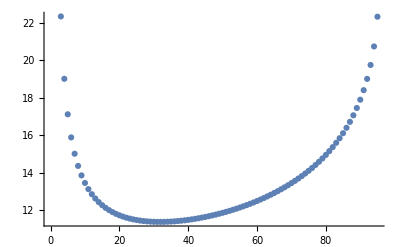

```mathematica
ListPlot[fsp2]
```

```mathematica
tp1=Table[D[B3[NS],g3]/.g3->fsp2[[NS]],{NS,1,95}]
```

{-11.6544,-10.0461,-10.3238,-10.9279,-11.5842,-12.2528,-12.9296,-13.6172,-14.319,-15.039,-15.7807,-16.5479,-17.3442,-18.1734,-19.0398,-19.9476,-20.9018,-21.9078,-22.9716,-24.1003,-25.3015,-26.5845,-27.9598,-29.4396,-31.0386,-32.7738,-34.666,-36.7401,-39.0266,-41.563,-44.3964,-47.586,-51.2082,-55.3629,-60.183,-65.8497,-72.6164,-80.8491,-91.0961,-104.218,-121.648,-145.961,-182.291,-242.579,-362.405,-716.91,-36788.8,743.19,366.948,243.095,181.394,144.406,119.732,102.08,88.809,78.4553,70.1416,63.31,57.5891,52.7217,48.5243,44.8623,41.6349,38.7647,36.1919,33.8688,31.7577,29.8278,28.0537,26.4147,24.8934,23.475,22.1471,20.8989,19.7213,18.6061,17.5463,16.5358,15.5687,14.6402,13.7456,12.8805,12.041,11.223,10.4227,9.63591,8.85846,8.08547,7.3112,6.52836,5.72696,4.89187,3.99697,2.9867,1.67667}

```mathematica
tp2=Table[ηTT/.etasf/.same/.g3->fsp2[[NS]],{NS,1,95}]
```

{-5.21458,-6.91039,-6.62895,-6.24217,-5.93018,-5.68361,-5.48391,-5.31768,-5.17594,-5.05261,-4.94347,-4.84552,-4.75653,-4.67486,-4.59921,-4.52861,-4.46226,-4.39953,-4.33991,-4.28296,-4.22833,-4.17572,-4.12488,-4.07559,-4.02767,-3.98096,-3.9353,-3.89059,-3.8467,-3.80355,-3.76103,-3.71908,-3.67762,-3.6366,-3.59594,-3.5556,-3.51552,-3.47566,-3.43598,-3.39644,-3.35699,-3.3176,-3.27825,-3.23889,-3.19949,-3.16002,-3.12046,-3.08078,-3.04094,-3.00092,-2.96069,-2.92022,-2.87949,-2.83846,-2.79711,-2.75541,-2.71333,-2.67084,-2.6279,-2.58448,-2.54056,-2.49608,-2.45102,-2.40533,-2.35897,-2.3119,-2.26406,-2.2154,-2.16587,-2.1154,-2.06393,-2.01139,-1.95768,-1.90272,-1.84642,-1.78865,-1.7293,-1.66822,-1.60524,-1.54018,-1.47281,-1.40289,-1.33011,-1.25409,-1.1744,-1.09046,-1.00157,-0.906814,-0.804934,-0.694188,-0.57199,-0.434217,-0.273508,-0.0739446,0.217501}

```mathematica
tp3=Table[ησ/.etasf/.same/.g3->fsp2[[NS]],{NS,1,95}]
```

{10.7811,5.053,1.35947,-0.897729,-2.49892,-3.75746,-4.81276,-5.73593,-6.56731,-7.33167,-8.04523,-8.71908,-9.36115,-9.97726,-10.5718,-11.1482,-11.7091,-12.2566,-12.7925,-13.3182,-13.8349,-14.3436,-14.8451,-15.3401,-15.8293,-16.3131,-16.7921,-17.2666,-17.737,-18.2036,-18.6667,-19.1265,-19.5833,-20.0372,-20.4884,-20.9371,-21.3835,-21.8275,-22.2694,-22.7093,-23.1473,-23.5834,-24.0177,-24.4503,-24.8812,-25.3106,-25.7384,-26.1648,-26.5897,-27.0131,-27.4353,-27.856,-28.2754,-28.6936,-29.1104,-29.526,-29.9403,-30.3534,-30.7652,-31.1758,-31.5851,-31.9932,-32.4,-32.8055,-33.2098,-33.6127,-34.0144,-34.4146,-34.8135,-35.2109,-35.6068,-36.0012,-36.394,-36.7852,-37.1745,-37.5621,-37.9477,-38.3313,-38.7126,-39.0916,-39.468,-39.8416,-40.2121,-40.5793,-40.9426,-41.3016,-41.6556,-42.0038,-42.345,-42.6776,-42.9993,-43.3062,-43.5916,-43.8409,-44.0055}

```mathematica
tp4=Table[ηS/.etasf/.same/.g3->fsp2[[NS]],{NS,1,95}]
```

{25.2266,19.6152,15.5574,13.3144,11.9249,10.9739,10.2759,9.73752,9.30683,8.95247,8.65442,8.39921,8.17743,7.98231,7.80883,7.65316,7.51237,7.38414,7.26662,7.15832,7.05799,6.96464,6.87741,6.7956,6.71858,6.64585,6.57696,6.51153,6.4492,6.3897,6.33277,6.27816,6.22568,6.17515,6.12641,6.0793,6.03371,5.9895,5.94657,5.90482,5.86417,5.82453,5.78583,5.74799,5.71095,5.67466,5.63906,5.60409,5.56971,5.53588,5.50254,5.46967,5.43722,5.40516,5.37346,5.34207,5.31098,5.28014,5.24954,5.21914,5.18891,5.15883,5.12886,5.09899,5.06918,5.03942,5.00966,4.97988,4.95006,4.92016,4.89015,4.86001,4.82968,4.79915,4.76836,4.73728,4.70585,4.67402,4.64174,4.60894,4.57553,4.54144,4.50655,4.47075,4.43388,4.39576,4.35614,4.31474,4.27114,4.22477,4.17478,4.11983,4.05753,3.98269,3.87804}

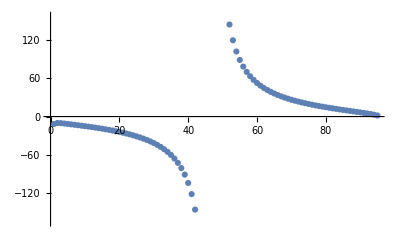

```mathematica
ListPlot[tp1]
```

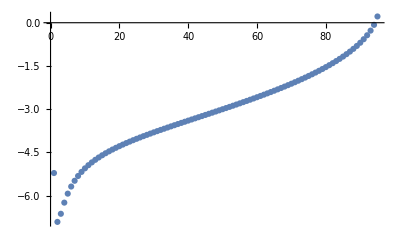

```mathematica
ListPlot[tp2]
```

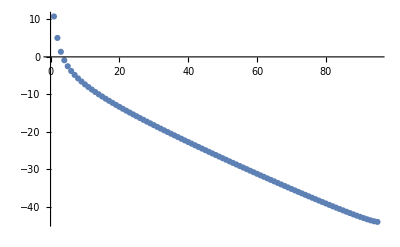

```mathematica
ListPlot[tp3]
```

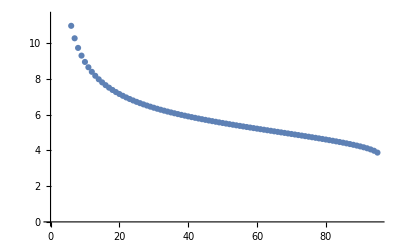

```mathematica
ListPlot[tp4]
```

```mathematica
(* the negative fixed point *)
```

```mathematica
NSolve[(B3[1])==0,g3]
NSolve[(B3[2])==0,g3]
NSolve[(B3[3])==0,g3]
NSolve[(B3[4])==0,g3]
```

{{g3→53.393},{g3→1.15771+16.074 ⅈ},{g3→1.15771-16.074 ⅈ},{g3→-13.8815},{g3→0.}}

{{g3→29.7842},{g3→-19.0491},{g3→-3.90898+15.1076 ⅈ},{g3→-3.90898-15.1076 ⅈ},{g3→0.}}

{{g3→-30.0025},{g3→22.3477},{g3→-5.60947+11.4435 ⅈ},{g3→-5.60947-11.4435 ⅈ},{g3→0.}}

{{g3→-41.5492},{g3→19.0164},{g3→-5.32477+9.29497 ⅈ},{g3→-5.32477-9.29497 ⅈ},{g3→0.}}

```mathematica
fsnb=Table[NSolve[(B3[NS])==0,g3][[1,1,2]],{NS,3,46}]
```

{-30.0025,-41.5492,-50.8463,-58.3761,-64.7103,-70.2374,-75.2154,-79.8206,-84.1788,-88.3834,-92.5067,-96.6074,-100.735,-104.935,-109.247,-113.711,-118.367,-123.258,-128.428,-133.925,-139.806,-146.134,-152.982,-160.437,-168.602,-177.604,-187.594,-198.766,-211.359,-225.683,-242.14,-261.267,-283.793,-310.738,-343.569,-384.486,-436.932,-506.63,-603.83,-748.904,-988.933,-1462.81,-2838.01,-58066.3}

```mathematica
fsn=Join[{-13.881523450149748},{-19.049077476150778},fsnb]
```

{-13.8815,-19.0491,-30.0025,-41.5492,-50.8463,-58.3761,-64.7103,-70.2374,-75.2154,-79.8206,-84.1788,-88.3834,-92.5067,-96.6074,-100.735,-104.935,-109.247,-113.711,-118.367,-123.258,-128.428,-133.925,-139.806,-146.134,-152.982,-160.437,-168.602,-177.604,-187.594,-198.766,-211.359,-225.683,-242.14,-261.267,-283.793,-310.738,-343.569,-384.486,-436.932,-506.63,-603.83,-748.904,-988.933,-1462.81,-2838.01,-58066.3}

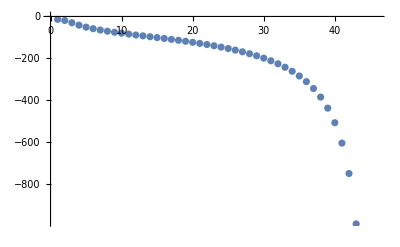

```mathematica
ListPlot[fsn]
```

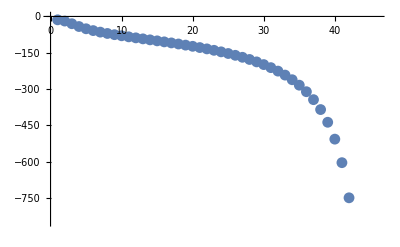

-Graphics-

```mathematica
tn1=Table[D[B3[NS],g3]/.g3->fsn[[NS]],{NS,1,46}]
```

{-3.84995,-3.55397,-5.0553,-7.31272,-8.79589,-9.70544,-10.2872,-10.6761,-10.9448,-11.1344,-11.2694,-11.3654,-11.4324,-11.4774,-11.5053,-11.5197,-11.523,-11.5173,-11.5041,-11.4846,-11.4596,-11.43,-11.3962,-11.3589,-11.3184,-11.2751,-11.2291,-11.1808,-11.1304,-11.0779,-11.0236,-10.9676,-10.9099,-10.8507,-10.79,-10.7278,-10.6643,-10.5995,-10.5334,-10.4659,-10.3973,-10.3274,-10.2562,-10.1839,-10.1103,-10.0355}

```mathematica
tn2=Table[ηTT/.etasf/.same/.g3->fsn[[NS]],{NS,1,46}]
```

{3.26741,4.62289,6.66334,7.78812,8.19788,8.33173,8.35584,8.33217,8.28617,8.22924,8.16688,8.10185,8.0356,7.96891,7.90219,7.83566,7.76941,7.70348,7.63788,7.5726,7.50761,7.44287,7.37836,7.31404,7.24987,7.18584,7.1219,7.05802,6.9942,6.93038,6.86657,6.80272,6.73883,6.67487,6.61082,6.54666,6.48238,6.41796,6.35338,6.28862,6.22368,6.15853,6.09316,6.02754,5.96168,5.89554}

```mathematica
tn3=Table[ησ/.etasf/.same/.g3->fsn[[NS]],{NS,1,46}]
```

{-0.309741,-2.01681,-2.84956,-2.52164,-2.16808,-2.00676,-2.00532,-2.11722,-2.30871,-2.55718,-2.84749,-3.16928,-3.51528,-3.88028,-4.26047,-4.65297,-5.05559,-5.46665,-5.88482,-6.30904,-6.73845,-7.17237,-7.61021,-8.05152,-8.49589,-8.94299,-9.39254,-9.84431,-10.2981,-10.7537,-11.211,-11.6698,-12.1301,-12.5917,-13.0546,-13.5186,-13.9838,-14.45,-14.9171,-15.3853,-15.8544,-16.3243,-16.7951,-17.2667,-17.7392,-18.2124}

```mathematica
tn4=Table[ηS/.etasf/.same/.g3->fsn[[NS]],{NS,1,46}]
```

{-6.48804,-7.27274,-7.16492,-5.71569,-4.28654,-3.17668,-2.33507,-1.6868,-1.17608,-0.764828,-0.427144,-0.145109,0.09395,0.299203,0.477423,0.633712,0.77198,0.895269,1.00598,1.10603,1.19698,1.2801,1.35642,1.42682,1.49204,1.55268,1.60928,1.66228,1.71207,1.75898,1.80331,1.84532,1.88522,1.92322,1.95949,1.99418,2.02744,2.0594,2.09015,2.11981,2.14847,2.1762,2.2031,2.22921,2.25462,2.27937}

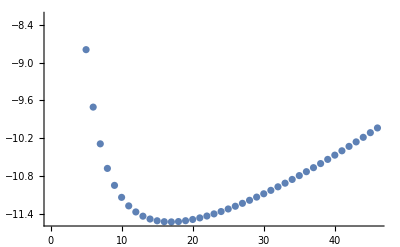

```mathematica
ListPlot[tn1]
```

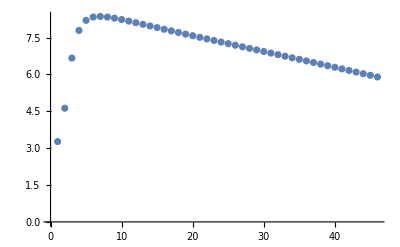

```mathematica
ListPlot[tn2]
```

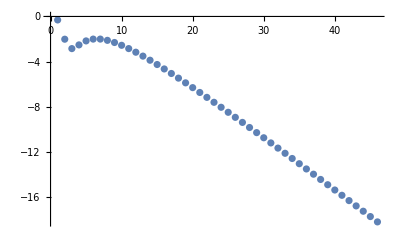

```mathematica
ListPlot[tn3]
```

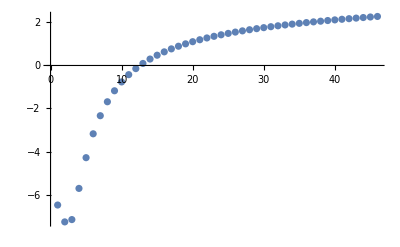

```mathematica
ListPlot[tn4]
```

```mathematica
(* the other positive fixed point *)
```

```mathematica
NSolve[(B3[1])==0,g3]
NSolve[(B3[2])==0,g3]
NSolve[(B3[3])==0,g3]
NSolve[(B3[4])==0,g3]
```

{{g3→53.393},{g3→1.15771+16.074 ⅈ},{g3→1.15771-16.074 ⅈ},{g3→-13.8815},{g3→0.}}

{{g3→29.7842},{g3→-19.0491},{g3→-3.90898+15.1076 ⅈ},{g3→-3.90898-15.1076 ⅈ},{g3→0.}}

{{g3→-30.0025},{g3→22.3477},{g3→-5.60947+11.4435 ⅈ},{g3→-5.60947-11.4435 ⅈ},{g3→0.}}

{{g3→-41.5492},{g3→19.0164},{g3→-5.32477+9.29497 ⅈ},{g3→-5.32477-9.29497 ⅈ},{g3→0.}}

```mathematica
fsp2=Table[NSolve[(B3[NS])==0,g3][[1,1,2]],{NS,47,95}]
```

{3105.61,1502.62,986.68,731.956,580.104,479.248,407.372,353.54,311.703,278.244,250.867,228.046,208.725,192.15,177.771,165.175,154.044,144.135,135.252,127.242,119.979,113.36,107.3,101.729,96.5872,91.8238,87.396,83.2669,79.4044,75.7807,72.3713,69.1547,66.1118,63.2253,60.4799,57.8612,55.3564,52.9532,50.6398,48.4048,46.2367,44.1231,42.0503,40.0022,37.9575,35.8854,33.7344,31.3962,28.5137}

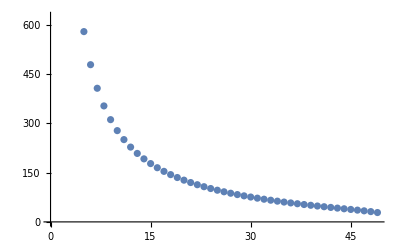

```mathematica
ListPlot[fsp2]
```

```mathematica
tnp21=Table[D[B3[i-46],g3]/.g3->fsp2[[i-46]],{i,47,95}]
```

{-5012.28,2470.76,764.131,422.592,283.858,210.36,165.378,135.219,113.684,97.5828,85.1138,75.1878,67.1085,60.4109,54.7733,49.9663,45.8218,42.2141,39.0473,36.2471,33.755,31.5243,29.5172,27.7032,26.0568,24.5571,23.1863,21.9299,20.775,19.711,18.7286,17.8199,16.9781,16.1972,15.4719,14.7979,14.1711,13.5881,13.0461,12.5426,12.0753,11.6428,11.2438,10.8776,10.5444,10.2453,9.98364,9.76746,9.62387}

```mathematica
tnp22=Table[ηTT/.etasf/.same/.g3->fsp2[[NS-46]],{NS,47,95}]
```

{5.82912,5.76239,5.69535,5.62796,5.56022,5.4921,5.42359,5.35466,5.2853,5.21548,5.14518,5.07436,5.00302,4.93112,4.85862,4.78551,4.71174,4.63728,4.56208,4.48612,4.40934,4.33169,4.25312,4.17358,4.09299,4.01128,3.92838,3.84421,3.75865,3.67161,3.58295,3.49254,3.40022,3.3058,3.20906,3.10974,3.00755,2.90212,2.793,2.67963,2.56131,2.4371,2.30578,2.16559,2.01394,1.84672,1.65657,1.42756,1.10668}

```mathematica
tnp23=Table[ησ/.etasf/.same/.g3->fsp2[[NS-46]],{NS,47,95}]
```

{-18.6864,-19.1611,-19.6366,-20.1128,-20.5898,-21.0675,-21.546,-22.0252,-22.5051,-22.9858,-23.4672,-23.9495,-24.4325,-24.9163,-25.4009,-25.8863,-26.3726,-26.8598,-27.3479,-27.837,-28.327,-28.818,-29.3102,-29.8034,-30.2978,-30.7935,-31.2905,-31.7888,-32.2886,-32.79,-33.2931,-33.798,-34.3048,-34.8138,-35.3251,-35.839,-36.3558,-36.8757,-37.3992,-37.9269,-38.4593,-38.9974,-39.5422,-40.0955,-40.6595,-41.2381,-41.838,-42.4739,-43.1943}

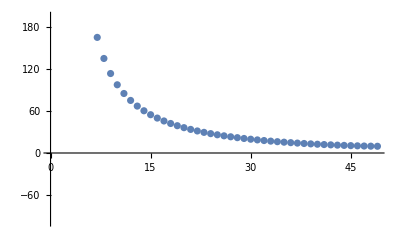

```mathematica
ListPlot[tnp21]
```

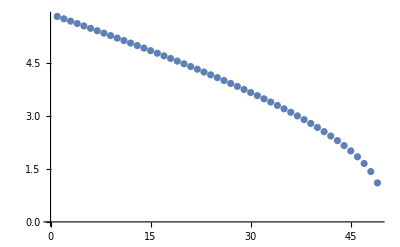

```mathematica
ListPlot[tnp22]
```

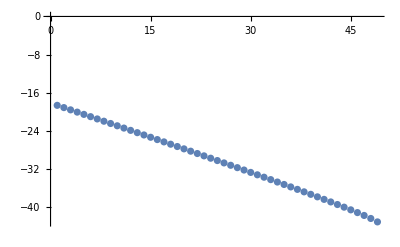

```mathematica
ListPlot[tnp23]
```

```mathematica
(* semiperturbative *)
```

```mathematica
B3sp[NS_]=βg3/.etasp/.same//Simplify
```

(g3 (g3^2 (-1287+74 NS)+270 g3 (4+NS) π+12960 π^2))/(6480 π^2)

```mathematica
fpsp1[NS_]=Solve[B3sp[NS]==0,g3][[3,1,2]]
fpsp2[NS_]=Solve[B3sp[NS]==0,g3][[2,1,2]]
```

(9 (-60-15 NS+√5 √(41904-2008 NS+45 NS^2)) π)/(-1287+74 NS)

(9 (-60-15 NS-√5 √(41904-2008 NS+45 NS^2)) π)/(-1287+74 NS)

```mathematica
NSolve[-1287+74 NS==0,NS]
```

{{NS→17.3919}}

```mathematica
Limit[fpsp1[NS],NS->Infinity]
Limit[fpsp2[NS],NS->Infinity]
```

0

-(135 π)/37

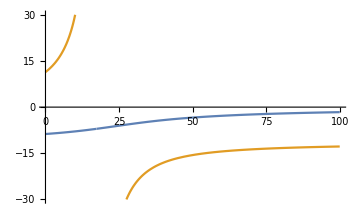

```mathematica
Plot[{fpsp1[NS],fpsp2[NS]},{NS,0,100},PlotRange->{-30,30}]
```

```mathematica
fpsp1[1]//N
fpsp2[1]//N
```

-8.66839

12.1648

```mathematica
(* the positive fp *)
```

```mathematica
tp1=Table[D[B3sp[NS],g3]/.g3->fpsp2[NS]//N,{NS,1,100}]
```

{-4.8067,-5.03962,-5.30866,-5.62225,-5.99163,-6.43199,-6.96442,-7.61907,-8.44053,-9.49757,-10.9022,-12.8494,-15.7121,-20.3034,-28.7956,-49.6053,-177.055,114.966,43.9234,27.4393,20.1537,16.0808,13.5041,11.7458,10.4847,9.54845,8.83658,8.28629,7.8564,7.51868,7.25317,7.04529,6.88418,6.76152,6.67088,6.60717,6.56631,6.54501,6.54056,6.55073,6.57367,6.60779,6.65178,6.70451,6.76501,6.83243,6.90607,6.98529,7.06954,7.15835,7.25128,7.34797,7.44808,7.55131,7.65741,7.76613,7.87727,7.99064,8.10607,8.22339,8.34248,8.46321,8.58546,8.70912,8.8341,8.96032,9.08769,9.21613,9.34559,9.476,9.60731,9.73945,9.87238,10.0061,10.1404,10.2755,10.4112,10.5474,10.6843,10.8216,10.9595,11.0979,11.2367,11.3759,11.5156,11.6557,11.7961,11.9369,12.0781,12.2195,12.3613,12.5034,12.6458,12.7884,12.9313,13.0745,13.2179,13.3616,13.5054,13.6495}

```mathematica
tp2=Table[ηTT/.etasp/.same/.g3->fpsp2[NS]//N,{NS,1,100}]
```

{-3.2806,-3.34989,-3.42743,-3.51488,-3.61445,-3.72905,-3.86273,-4.02119,-4.21281,-4.45042,-4.75481,-5.16213,-5.74124,-6.64212,-8.26521,-12.1614,-35.7097,18.0251,4.86179,1.74663,0.32205,-0.514893,-1.0805,-1.4996,-1.83139,-2.10754,-2.34647,-2.55964,-2.75452,-2.93613,-3.10802,-3.27268,-3.43195,-3.58717,-3.73937,-3.88929,-4.03753,-4.18453,-4.33062,-4.47607,-4.62108,-4.76582,-4.9104,-5.05491,-5.19942,-5.344,-5.48868,-5.63348,-5.77844,-5.92357,-6.06887,-6.21436,-6.36004,-6.50591,-6.65197,-6.79821,-6.94463,-7.09124,-7.23802,-7.38497,-7.53208,-7.67935,-7.82678,-7.97435,-8.12206,-8.26992,-8.4179,-8.56601,-8.71425,-8.8626,-9.01106,-9.15963,-9.30831,-9.45708,-9.60595,-9.75491,-9.90397,-10.0531,-10.2023,-10.3516,-10.501,-10.6504,-10.8,-10.9495,-11.0992,-11.2489,-11.3987,-11.5485,-11.6984,-11.8483,-11.9983,-12.1483,-12.2984,-12.4486,-12.5987,-12.749,-12.8992,-13.0495,-13.1999,-13.3503}

```mathematica
tp3=Table[ησ/.etasp/.same/.g3->fpsp2[NS]//N,{NS,1,100}]
```

{2.68901,3.58092,4.61145,5.81308,7.22889,8.9173,10.9594,13.471,16.6235,20.6813,26.0748,33.5538,44.552,62.1944,94.8324,174.82,664.75,-457.838,-184.748,-121.39,-93.3944,-77.7488,-67.8552,-61.1087,-56.2738,-52.6884,-49.966,-47.8653,-46.228,-44.9454,-43.9409,-43.1585,-42.5562,-42.1021,-41.7715,-41.5447,-41.4062,-41.3431,-41.3451,-41.4036,-41.5114,-41.6625,-41.8517,-42.0747,-42.3277,-42.6076,-42.9115,-43.237,-43.582,-43.9446,-44.3232,-44.7164,-45.1228,-45.5414,-45.971,-46.4108,-46.8601,-47.3179,-47.7837,-48.2569,-48.737,-49.2234,-49.7157,-50.2135,-50.7164,-51.2241,-51.7363,-52.2527,-52.773,-53.297,-53.8245,-54.3552,-54.889,-55.4257,-55.9651,-56.5071,-57.0516,-57.5984,-58.1473,-58.6984,-59.2514,-59.8063,-60.363,-60.9213,-61.4813,-62.0429,-62.6058,-63.1702,-63.736,-64.303,-64.8712,-65.4406,-66.0111,-66.5827,-67.1553,-67.7289,-68.3035,-68.8789,-69.4552,-70.0324}

```mathematica
tp4=Table[ηS/.etasp/.same/.g3->fpsp2[NS]//N,{NS,1,100}]
```

{6.77631,7.27735,7.85193,8.51683,9.29429,10.2144,11.3187,12.6668,14.3463,16.4927,19.326,23.2296,28.9359,38.0412,54.8114,95.7711,346.109,-227.117,-87.5123,-55.0187,-40.5782,-32.4383,-27.2285,-23.6187,-20.9778,-18.9678,-17.3915,-16.1258,-15.09,-14.229,-13.5038,-12.8862,-12.355,-11.8943,-11.4917,-11.1375,-10.824,-10.545,-10.2954,-10.0712,-9.86876,-9.68538,-9.51862,-9.36645,-9.22715,-9.09924,-8.98147,-8.87274,-8.77209,-8.67872,-8.59189,-8.51098,-8.43542,-8.36474,-8.29849,-8.23629,-8.17779,-8.12269,-8.07071,-8.0216,-7.97514,-7.93113,-7.88939,-7.84975,-7.81206,-7.77619,-7.74201,-7.70941,-7.67829,-7.64854,-7.62009,-7.59285,-7.56675,-7.54172,-7.5177,-7.49463,-7.47245,-7.45112,-7.43059,-7.41082,-7.39176,-7.37338,-7.35564,-7.33852,-7.32197,-7.30598,-7.29051,-7.27555,-7.26106,-7.24703,-7.23343,-7.22024,-7.20745,-7.19504,-7.183,-7.1713,-7.15993,-7.14888,-7.13814,-7.12769}

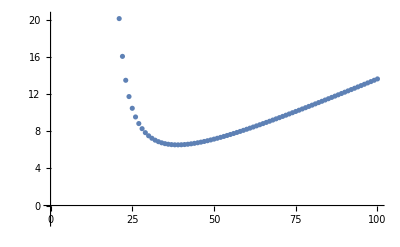

```mathematica
ListPlot[tp1]
```

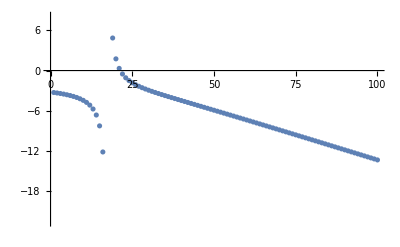

```mathematica
ListPlot[tp2]
```

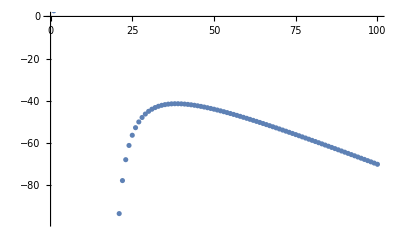

```mathematica
ListPlot[tp3]
```

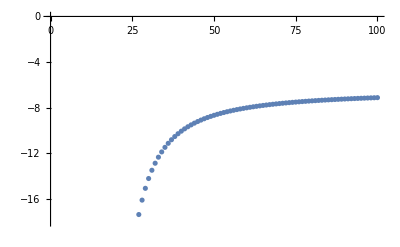

```mathematica
ListPlot[tp4]
```

```mathematica
(* the negative fixed point *)
```

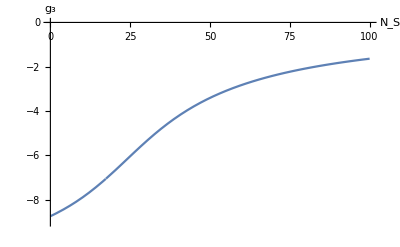

```mathematica
Plot[fpsp1[NS],{NS,0,100},PlotRange->{-9,0},AxesLabel->{Subscript[N, S],Subscript[g, 3]},LabelStyle->{FontSize->16}]
```

```mathematica
tp1=Table[D[B3sp[NS],g3]/.g3->fpsp1[NS]//N,{NS,1,100}]
```

{-3.42516,-3.31595,-3.20895,-3.10428,-3.0021,-2.90253,-2.80573,-2.71186,-2.62107,-2.53351,-2.44933,-2.36869,-2.29171,-2.21854,-2.14928,-2.08402,-2.02285,-1.9658,-1.9129,-1.86413,-1.81944,-1.77877,-1.742,-1.709,-1.67961,-1.65363,-1.63088,-1.61113,-1.59417,-1.57977,-1.56772,-1.55778,-1.54976,-1.54346,-1.53869,-1.53527,-1.53305,-1.53189,-1.53165,-1.5322,-1.53346,-1.5353,-1.53767,-1.54047,-1.54364,-1.54712,-1.55087,-1.55483,-1.55896,-1.56324,-1.56763,-1.5721,-1.57663,-1.58121,-1.58581,-1.59042,-1.59503,-1.59963,-1.6042,-1.60874,-1.61325,-1.61771,-1.62212,-1.62649,-1.6308,-1.63505,-1.63924,-1.64337,-1.64744,-1.65145,-1.65539,-1.65927,-1.66308,-1.66683,-1.67052,-1.67415,-1.67771,-1.68121,-1.68465,-1.68803,-1.69135,-1.69461,-1.69781,-1.70096,-1.70405,-1.70708,-1.71006,-1.71299,-1.71587,-1.7187,-1.72147,-1.7242,-1.72688,-1.72952,-1.73211,-1.73465,-1.73715,-1.73961,-1.74203,-1.7444}

```mathematica
tp2=Table[ηTT/.etasp/.same/.g3->fpsp1[NS]//N,{NS,1,100}]
```

{2.33769,2.20415,2.0718,1.94072,1.81101,1.68279,1.55617,1.43127,1.30822,1.18716,1.06824,0.9516,0.837396,0.72578,0.616907,0.510927,0.407983,0.308212,0.211735,0.11866,0.0290741,-0.0569546,-0.139383,-0.21819,-0.293383,-0.36499,-0.433065,-0.497681,-0.55893,-0.61692,-0.671774,-0.72362,-0.772598,-0.818847,-0.862512,-0.903734,-0.942654,-0.979409,-1.01413,-1.04694,-1.07797,-1.10733,-1.13512,-1.16145,-1.18641,-1.21009,-1.23257,-1.25393,-1.27425,-1.29359,-1.31201,-1.32956,-1.34631,-1.36231,-1.37759,-1.3922,-1.40618,-1.41958,-1.43241,-1.44472,-1.45653,-1.46788,-1.47878,-1.48926,-1.49935,-1.50907,-1.51842,-1.52744,-1.53615,-1.54454,-1.55265,-1.56049,-1.56806,-1.57539,-1.58247,-1.58933,-1.59598,-1.60242,-1.60866,-1.61471,-1.62058,-1.62629,-1.63182,-1.6372,-1.64242,-1.6475,-1.65245,-1.65725,-1.66193,-1.66648,-1.67092,-1.67524,-1.67945,-1.68355,-1.68756,-1.69146,-1.69527,-1.69899,-1.70261,-1.70616}

```mathematica
tp3=Table[ησ/.etasp/.same/.g3->fpsp1[NS]//N,{NS,1,100}]
```

{-1.91614,-2.35616,-2.78751,-3.20965,-3.62202,-4.02406,-4.41517,-4.79474,-5.16216,-5.51681,-5.85809,-6.1854,-6.49819,-6.79594,-7.0782,-7.34457,-7.59477,-7.82858,-8.04593,-8.24684,-8.43149,-8.60014,-8.75322,-8.89125,-9.01486,-9.12476,-9.22174,-9.30663,-9.3803,-9.44363,-9.49749,-9.54274,-9.58021,-9.61068,-9.63489,-9.65352,-9.66722,-9.67656,-9.68207,-9.68423,-9.68347,-9.68018,-9.6747,-9.66733,-9.65834,-9.64798,-9.63645,-9.62395,-9.61062,-9.59662,-9.58207,-9.56708,-9.55175,-9.53615,-9.52036,-9.50445,-9.48846,-9.47245,-9.45645,-9.44049,-9.42462,-9.40885,-9.39321,-9.37771,-9.36236,-9.34719,-9.33221,-9.31741,-9.30282,-9.28842,-9.27424,-9.26026,-9.2465,-9.23295,-9.21962,-9.2065,-9.19359,-9.1809,-9.16842,-9.15615,-9.14408,-9.13222,-9.12056,-9.10909,-9.09783,-9.08675,-9.07587,-9.06517,-9.05465,-9.04432,-9.03416,-9.02417,-9.01435,-9.0047,-8.99521,-8.98588,-8.97671,-8.96769,-8.95882,-8.9501}

```mathematica
tp4=Table[ηS/.etasp/.same/.g3->fpsp1[NS]//N,{NS,1,100}]
```

{-4.82866,-4.78833,-4.7463,-4.7025,-4.65689,-4.60938,-4.55993,-4.50849,-4.45501,-4.39948,-4.34188,-4.2822,-4.22048,-4.15674,-4.09107,-4.02355,-3.9543,-3.88347,-3.81123,-3.73778,-3.66334,-3.58814,-3.51244,-3.4365,-3.36057,-3.28491,-3.20978,-3.13539,-3.06196,-2.98969,-2.91874,-2.84926,-2.78135,-2.71513,-2.65065,-2.58797,-2.52712,-2.46811,-2.41095,-2.35562,-2.30211,-2.25037,-2.20038,-2.15209,-2.10545,-2.06042,-2.01693,-1.97495,-1.93441,-1.89526,-1.85745,-1.82093,-1.78564,-1.75154,-1.71858,-1.68671,-1.65588,-1.62606,-1.5972,-1.56926,-1.54221,-1.516,-1.49061,-1.46599,-1.44212,-1.41897,-1.39651,-1.3747,-1.35353,-1.33296,-1.31298,-1.29356,-1.27468,-1.25632,-1.23846,-1.22107,-1.20415,-1.18767,-1.17162,-1.15599,-1.14075,-1.12589,-1.1114,-1.09727,-1.08348,-1.07003,-1.05689,-1.04407,-1.03154,-1.01931,-1.00735,-0.995661,-0.984236,-0.973064,-0.962136,-0.951446,-0.940986,-0.930749,-0.920727,-0.910915}

```mathematica
Export["data_roberto_g3",Table[{i,fpsp1[i]},{i,0,100}]//N,"Table"];
Export["data_roberto_critical_exponent.dat",Table[{i,-tp1[[i]]},{i,1,100}],"Table"];
Export["data_roberto_eta_TT.dat",Table[{i,tp2[[i]]},{i,1,100}],"Table"];
Export["data_roberto_eta_sigma.dat",Table[{i,tp3[[i]]},{i,1,100}],"Table"];
Export["data_roberto_eta_s.dat",Table[{i,tp4[[i]]},{i,1,100}],"Table"];
```

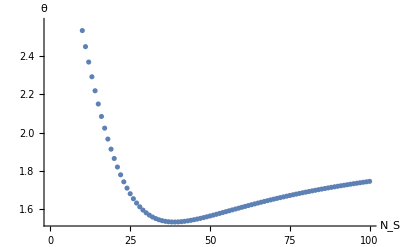

```mathematica
ListPlot[-tp1,AxesLabel->{Subscript[N, S],θ},LabelStyle->{FontSize->16}]
```

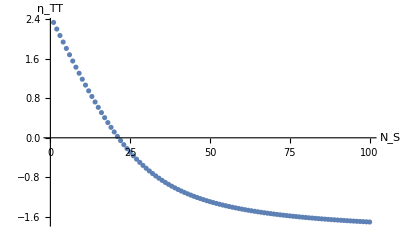

```mathematica
ListPlot[tp2,AxesLabel->{Subscript[N, S],Subscript[η, TT]},LabelStyle->{FontSize->16}]
```

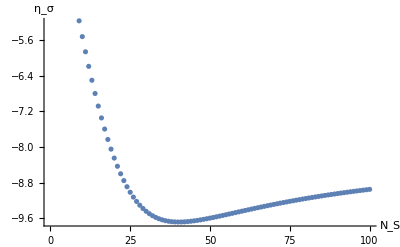

```mathematica
ListPlot[tp3,AxesLabel->{Subscript[N, S],Subscript[η, σ]},LabelStyle->{FontSize->16}]
```

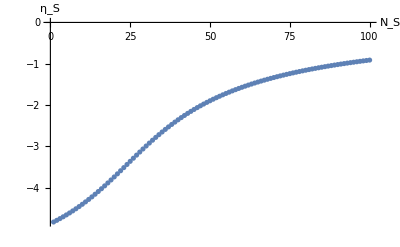

```mathematica
ListPlot[tp4,AxesLabel->{Subscript[N, S],Subscript[η, S]},LabelStyle->{FontSize->16}]
```